```mathematica
Normalization =1/(√3); 
G2Roots= Normalization Flatten[Table[If[a+b+c==0&&(a^2+b^2+c^2==2||a^2+b^2+c^2==6),{a,b,c},Nothing],{a,-2,2},{b,-2,2},{c,-2,2}],2];
G2LongRoots = Normalization Flatten[Table[If[a+b+c==0&&(a^2+b^2+c^2==6),{a,b,c},Nothing],{a,-2,2},{b,-2,2},{c,-2,2}],2];
G2Lattice=1/3 Flatten[Table[If[a+b+c==0,{a,b,c},Nothing],{a,-2,2},{b,-2,2},{c,-2,2}],2];
G2Coroots = Table[2a/a.a,{a,G2Roots}];
G2SimpleRoots =Normalization  {{0,1,-1},{1,-2,1}};
G2SimpleCoroots = Table[2a/a.a,{a,G2SimpleRoots}];
l[ϵ1_,ϵ2_,σ1_,σ2_,σ3_,k1_,k2_,k3_,a1_,a2_,a3_]:=Product[Which[{k1,k2,k3}.{a1,a2,a3}<0&&i+j≤-{k1,k2,k3}.{a1,a2,a3}-1,(-ϵ1 i-ϵ2 j+{a1,a2,a3}.{σ1,σ2,σ3}),{k1,k2,k3}.{a1,a2,a3}>1&&i+j≤{k1,k2,k3}.{a1,a2,a3}-2,(ϵ1(i+1)+ϵ2(j+1)+{a1,a2,a3}.{σ1,σ2,σ3}),True,1],{i,0,2},{j,0,2}];
l[ϵ1_,ϵ2_,{σ1_,σ2_,σ3_},{k1_,k2_,k3_},{a1_,a2_,a3_}]:=l[ϵ1,ϵ2,σ1,σ2,σ3,k1,k2,k3,a1,a2,a3];
L[ϵ1_,ϵ2_,{σ1_,σ2_,σ3_},{k1_,k2_,k3_}]:=Product[l[ϵ1,ϵ2,{σ1,σ2,σ3},{k1,k2,k3},a],{a,G2Roots}]//Cancel;
Subscript[Ž, 1][ϵ1_,ϵ2_,{σ1_,σ2_,σ3_}]:=1/(-ϵ1 ϵ2)Sum[(1/((+ϵ1+ϵ2+{σ1,σ2,σ3}.a)({σ1,σ2,σ3}.a)Product[If[ 2b.a/a.a==1, {σ1,σ2,σ3}.b,1],{b,G2Roots}]))//Cancel,{a,G2LongRoots}];
σ:={σ1,σ2,σ3};
a:={a1,a2,a3};
F[{v1_,v2_,v3_}]:=F[v1,v2,v3]
F[v1_,v2_,v3_]:=1/(Product[If[a.{v1,v2,v3}==1,Abs[-a.σ]//Refine,1]If[a.{v1,v2,v3}==2,(-a.σ)^2(1+a.σ)^2,1]If[a.{v1,v2,v3}==3,(-a.σ)^3(1+a.σ)^4(2+a.σ)^2,1],{a,G2Roots}])//Cancel
$Assumptions=1>-2 σ1+σ2+σ3&&σ1+σ2-2 σ3>0&&σ1>σ3>0;
```

```mathematica
G2SimpleRoots[[1]]
```

{0,1/(√3),-1/(√3)}

```mathematica
L[1,-1,σ,{0,1/(√3),-1/(√3)}]
```

-1/9 (√3 σ1+√3 σ2-2 √3 σ3) (√3 σ1-2 √3 σ2+√3 σ3)

```mathematica
G2CorootLattice=Flatten[Table[a G2SimpleCoroots[[1]]+b G2SimpleCoroots[[2]],{a,-2,2},{b,-2,2}],1]
```

{{-2/(√3),4/(√3)-2 √3,-2/(√3)+2 √3},{-1/(√3),2/(√3)-2 √3,-1/(√3)+2 √3},{0,-2 √3,2 √3},{1/(√3),-2/(√3)-2 √3,1/(√3)+2 √3},{2/(√3),-4/(√3)-2 √3,2/(√3)+2 √3},{-2/(√3),4/(√3)-√3,-2/(√3)+√3},{-1/(√3),2/(√3)-√3,-1/(√3)+√3},{0,-√3,√3},{1/(√3),-2/(√3)-√3,1/(√3)+√3},{2/(√3),-4/(√3)-√3,2/(√3)+√3},{-2/(√3),4/(√3),-2/(√3)},{-1/(√3),2/(√3),-1/(√3)},{0,0,0},{1/(√3),-2/(√3),1/(√3)},{2/(√3),-4/(√3),2/(√3)},{-2/(√3),4/(√3)+√3,-2/(√3)-√3},{-1/(√3),2/(√3)+√3,-1/(√3)-√3},{0,√3,-√3},{1/(√3),-2/(√3)+√3,1/(√3)-√3},{2/(√3),-4/(√3)+√3,2/(√3)-√3},{-2/(√3),4/(√3)+2 √3,-2/(√3)-2 √3},{-1/(√3),2/(√3)+2 √3,-1/(√3)-2 √3},{0,2 √3,-2 √3},{1/(√3),-2/(√3)+2 √3,1/(√3)-2 √3},{2/(√3),-4/(√3)+2 √3,2/(√3)-2 √3}}

```mathematica
testroot=RandomChoice[G2LongRoots]
```

{-1/(√3),-1/(√3),2/(√3)}

```mathematica
L[ϵ1,ϵ2,{a1,a2},testroot]
```

-(a1-a2) (a1-a2-ϵ1) (a1-a2-ϵ2) (a1-a2-ϵ1-ϵ2)

```mathematica
L[ϵ1,-ϵ1,{a1,a2},testroot]
```

-(a1-a2)^2 (a1-a2-ϵ1) (a1-a2+ϵ1)

```mathematica
Subscript[Ž, 1][1,-1,{a1,a2,a3}]//Simplify
```

486/((a1+a2-2 a3)^2 (a1-2 a2+a3)^2 (-2 a1+a2+a3)^2)

```mathematica
z[n_,ϵ1_,ϵ2_,{σ1_,σ2_,σ3_}]:=1/(n^2 ϵ1 ϵ2)Sum[If[1/2 k.k + m1+m2 == n,(((ϵ1 m1+(ϵ1+ϵ2) m2+k.{σ1,σ2,σ3}+k.k/2(2ϵ1+ϵ2))(ϵ1 m1+(ϵ1+ϵ2) m2+k.{σ1,σ2,σ3}+k.k/2(2ϵ1+ϵ2)-n(ϵ1+ϵ2)))/L[ϵ1,ϵ1+ϵ2,{σ1,σ2,σ3},k])Subscript[Ž, m1][ϵ1,ϵ2,{σ1,σ2,σ3}+ϵ1 k]Subscript[Ž, m2][-ϵ2,ϵ1+ϵ2,{σ1,σ2,σ3}+ϵ1 k+ϵ2 k]/.Subscript[Ž, 0][x_,y_,z_]->1//Cancel,0],{k,G2CorootLattice},{m1,0,n-1},{m2,0,n-1}]
```

```mathematica
z[1,1,-1,σ]//Together
```

486/((σ1+σ2-2 σ3)^2 (2 σ1-σ2-σ3)^2 (σ1-2 σ2+σ3)^2)

```mathematica
Z1[σ1_,σ2_,σ3_]:=486/((σ1+σ2-2 σ3)^2 (2 σ1-σ2-σ3)^2 (σ1-2 σ2+σ3)^2);
Z1[{v1_,v2_,v3_}]:=Z1[v1,v2,v3];
```

```mathematica
1/(2^2 ϵ1 ϵ2)Sum[If[1/2 k.k == 2,((+k.σ+k.k/2(2ϵ1+ϵ2))(+k.σ+k.k/2(2ϵ1+ϵ2)-2(ϵ1+ϵ2)))/L[ϵ1,ϵ1+ϵ2,σ,k]//Cancel,0],{k,G2CorootLattice}]+1/(2^2 ϵ1 ϵ2)Sum[If[1/2 k.k == 1,((ϵ1 1+k.σ+k.k/2(2ϵ1+ϵ2))(ϵ1 1+k.σ+k.k/2(2ϵ1+ϵ2)-2(ϵ1+ϵ2)))/L[ϵ1,ϵ1+ϵ2,σ,k] Subscript[Ž, 1][ϵ1,ϵ2,σ+ϵ1 k]/.Subscript[Ž, 0][x_,y_,z_]->1//Cancel,0],{k,G2CorootLattice}]+1/(2^2 ϵ1 ϵ2)Sum[If[1/2 k.k == 1,((+(ϵ1+ϵ2) 1+k.σ+k.k/2(2ϵ1+ϵ2))(+(ϵ1+ϵ2) 1+k.σ+k.k/2(2ϵ1+ϵ2)-2(ϵ1+ϵ2)))/L[ϵ1,ϵ1+ϵ2,σ,k] Subscript[Ž, 1][-ϵ2,ϵ1+ϵ2,σ+ϵ1 k+ϵ2 k]/.Subscript[Ž, 0][x_,y_,z_]->1//Cancel,0],{k,G2CorootLattice}]+1/(2^2 ϵ1 ϵ2)((ϵ1 1+(ϵ1+ϵ2) 1)(ϵ1 1+(ϵ1+ϵ2) 1+-2(ϵ1+ϵ2)))/L[ϵ1,ϵ1+ϵ2,σ,{0,0,0}] Subscript[Ž, 1][ϵ1,ϵ2,σ]Subscript[Ž, 1][-ϵ2,ϵ1+ϵ2,σ]
```

-1/(4 ϵ1^2 ϵ2^3 (ϵ1+ϵ2))(2 ϵ1+ϵ2) (2 ϵ1+ϵ2-2 (ϵ1+ϵ2)) ((27 √3)/((σ1+σ2-2 σ3) (σ1-σ3) (2 σ1-σ2-σ3) (σ1-2 σ2+σ3) (-σ2+σ3) (-3 ϵ1+√3 σ1+√3 σ2-2 √3 σ3))-(27 √3)/((σ1+σ2-2 σ3) (σ1-σ3) (2 σ1-σ2-σ3) (σ2-σ3) (σ1-2 σ2+σ3) (3 ϵ1+√3 σ1+√3 σ2-2 √3 σ3))+(27 √3)/((σ1-σ2) (σ1+σ2-2 σ3) (σ1-σ3) (2 σ1-σ2-σ3) (σ1-2 σ2+σ3) (-3 ϵ1+2 √3 σ1-√3 σ2-√3 σ3))+(27 √3)/((σ1-σ2) (σ1+σ2-2 σ3) (σ1-σ3) (2 σ1-σ2-σ3) (σ1-2 σ2+σ3) (3 ϵ1+2 √3 σ1-√3 σ2-√3 σ3))+(27 √3)/((σ1-σ2) (σ1+σ2-2 σ3) (2 σ1-σ2-σ3) (σ2-σ3) (σ1-2 σ2+σ3) (-3 ϵ1+√3 σ1-2 √3 σ2+√3 σ3))+(27 √3)/((σ1-σ2) (σ1+σ2-2 σ3) (2 σ1-σ2-σ3) (σ2-σ3) (σ1-2 σ2+σ3) (3 ϵ1+√3 σ1-2 √3 σ2+√3 σ3))) ((27 √3)/((σ1+σ2-2 σ3) (σ1-σ3) (2 σ1-σ2-σ3) (σ1-2 σ2+σ3) (-σ2+σ3) (-3 ϵ1-3 ϵ2+√3 σ1+√3 σ2-2 √3 σ3))-(27 √3)/((σ1+σ2-2 σ3) (σ1-σ3) (2 σ1-σ2-σ3) (σ2-σ3) (σ1-2 σ2+σ3) (3 ϵ1+3 ϵ2+√3 σ1+√3 σ2-2 √3 σ3))+(27 √3)/((σ1-σ2) (σ1+σ2-2 σ3) (σ1-σ3) (2 σ1-σ2-σ3) (σ1-2 σ2+σ3) (-3 ϵ1-3 ϵ2+2 √3 σ1-√3 σ2-√3 σ3))+(27 √3)/((σ1-σ2) (σ1+σ2-2 σ3) (σ1-σ3) (2 σ1-σ2-σ3) (σ1-2 σ2+σ3) (3 ϵ1+3 ϵ2+2 √3 σ1-√3 σ2-√3 σ3))+(27 √3)/((σ1-σ2) (σ1+σ2-2 σ3) (2 σ1-σ2-σ3) (σ2-σ3) (σ1-2 σ2+σ3) (-3 ϵ1-3 ϵ2+√3 σ1-2 √3 σ2+√3 σ3))+(27 √3)/((σ1-σ2) (σ1+σ2-2 σ3) (2 σ1-σ2-σ3) (σ2-σ3) (σ1-2 σ2+σ3) (3 ϵ1+3 ϵ2+√3 σ1-2 √3 σ2+√3 σ3)))+1/(4 ϵ1 ϵ2)(-((354294 (54 ϵ1^5-90 √3 ϵ1^4 σ1+180 ϵ1^3 σ1^2-60 √3 ϵ1^2 σ1^3+30 ϵ1 σ1^4-2 √3 σ1^5+45 √3 ϵ1^4 σ2-180 ϵ1^3 σ1 σ2+90 √3 ϵ1^2 σ1^2 σ2-60 ϵ1 σ1^3 σ2+5 √3 σ1^4 σ2-15 √3 ϵ1^2 σ2^3+30 ϵ1 σ1 σ2^3-5 √3 σ1^2 σ2^3-6 ϵ1 σ2^4+2 √3 σ1 σ2^4+45 √3 ϵ1^4 σ3-180 ϵ1^3 σ1 σ3+90 √3 ϵ1^2 σ1^2 σ3-60 ϵ1 σ1^3 σ3+5 √3 σ1^4 σ3+180 ϵ1^3 σ2 σ3-180 √3 ϵ1^2 σ1 σ2 σ3+180 ϵ1 σ1^2 σ2 σ3-20 √3 σ1^3 σ2 σ3+45 √3 ϵ1^2 σ2^2 σ3-90 ϵ1 σ1 σ2^2 σ3+15 √3 σ1^2 σ2^2 σ3-6 ϵ1 σ2^3 σ3+2 √3 σ1 σ2^3 σ3-2 √3 σ2^4 σ3+45 √3 ϵ1^2 σ2 σ3^2-90 ϵ1 σ1 σ2 σ3^2+15 √3 σ1^2 σ2 σ3^2+54 ϵ1 σ2^2 σ3^2-18 √3 σ1 σ2^2 σ3^2+3 √3 σ2^3 σ3^2-15 √3 ϵ1^2 σ3^3+30 ϵ1 σ1 σ3^3-5 √3 σ1^2 σ3^3-6 ϵ1 σ2 σ3^3+2 √3 σ1 σ2 σ3^3+3 √3 σ2^2 σ3^3-6 ϵ1 σ3^4+2 √3 σ1 σ3^4-2 √3 σ2 σ3^4))/(ϵ1 ϵ2 (σ1-σ2) (√3 ϵ1-σ1+σ2) (σ1+σ2-2 σ3) (σ1-σ3) (2 σ1-σ2-σ3) (√3 ϵ1-σ1+2 σ2-σ3) (√3 ϵ1-σ1+σ3) (σ1-2 σ2+σ3) (2 √3 ϵ1-2 σ1+σ2+σ3) (√3 ϵ1-σ1-σ2+2 σ3) (3 ϵ2+√3 σ1+√3 σ2-2 √3 σ3) (6 ϵ1+3 ϵ2-√3 σ1+2 √3 σ2-√3 σ3) (3 ϵ2+√3 σ1-2 √3 σ2+√3 σ3) (3 ϵ1-2 √3 σ1+√3 σ2+√3 σ3) (3 ϵ1+3 ϵ2-2 √3 σ1+√3 σ2+√3 σ3) (6 ϵ1+3 ϵ2-2 √3 σ1+√3 σ2+√3 σ3) (6 ϵ1+3 ϵ2-√3 σ1-√3 σ2+2 √3 σ3)))-(354294 (54 ϵ1^5-45 √3 ϵ1^4 σ1+15 √3 ϵ1^2 σ1^3-6 ϵ1 σ1^4+90 √3 ϵ1^4 σ2-180 ϵ1^3 σ1 σ2+30 ϵ1 σ1^3 σ2-2 √3 σ1^4 σ2+180 ϵ1^3 σ2^2-90 √3 ϵ1^2 σ1 σ2^2+5 √3 σ1^3 σ2^2+60 √3 ϵ1^2 σ2^3-60 ϵ1 σ1 σ2^3+30 ϵ1 σ2^4-5 √3 σ1 σ2^4+2 √3 σ2^5-45 √3 ϵ1^4 σ3+180 ϵ1^3 σ1 σ3-45 √3 ϵ1^2 σ1^2 σ3-6 ϵ1 σ1^3 σ3+2 √3 σ1^4 σ3-180 ϵ1^3 σ2 σ3+180 √3 ϵ1^2 σ1 σ2 σ3-90 ϵ1 σ1^2 σ2 σ3-2 √3 σ1^3 σ2 σ3-90 √3 ϵ1^2 σ2^2 σ3+180 ϵ1 σ1 σ2^2 σ3-15 √3 σ1^2 σ2^2 σ3-60 ϵ1 σ2^3 σ3+20 √3 σ1 σ2^3 σ3-5 √3 σ2^4 σ3-45 √3 ϵ1^2 σ1 σ3^2+54 ϵ1 σ1^2 σ3^2-3 √3 σ1^3 σ3^2-90 ϵ1 σ1 σ2 σ3^2+18 √3 σ1^2 σ2 σ3^2-15 √3 σ1 σ2^2 σ3^2+15 √3 ϵ1^2 σ3^3-6 ϵ1 σ1 σ3^3-3 √3 σ1^2 σ3^3+30 ϵ1 σ2 σ3^3-2 √3 σ1 σ2 σ3^3+5 √3 σ2^2 σ3^3-6 ϵ1 σ3^4+2 √3 σ1 σ3^4-2 √3 σ2 σ3^4))/(ϵ1 ϵ2 (σ1-σ2) (√3 ϵ1-σ1+σ2) (σ1+σ2-2 σ3) (√3 ϵ1+σ1+σ2-2 σ3) (2 σ1-σ2-σ3) (σ2-σ3) (√3 ϵ1+σ2-σ3) (2 √3 ϵ1-σ1+2 σ2-σ3) (σ1-2 σ2+σ3) (√3 ϵ1-2 σ1+σ2+σ3) (6 ϵ1+3 ϵ2+√3 σ1+√3 σ2-2 √3 σ3) (3 ϵ2+2 √3 σ1-√3 σ2-√3 σ3) (3 ϵ1-√3 σ1+2 √3 σ2-√3 σ3) (3 ϵ1+3 ϵ2-√3 σ1+2 √3 σ2-√3 σ3) (6 ϵ1+3 ϵ2-√3 σ1+2 √3 σ2-√3 σ3) (6 ϵ1+3 ϵ2-2 √3 σ1+√3 σ2+√3 σ3) (3 ϵ2-√3 σ1-√3 σ2+2 √3 σ3))+(354294 (54 ϵ1^5+45 √3 ϵ1^4 σ1-15 √3 ϵ1^2 σ1^3-6 ϵ1 σ1^4-90 √3 ϵ1^4 σ2-180 ϵ1^3 σ1 σ2+30 ϵ1 σ1^3 σ2+2 √3 σ1^4 σ2+180 ϵ1^3 σ2^2+90 √3 ϵ1^2 σ1 σ2^2-5 √3 σ1^3 σ2^2-60 √3 ϵ1^2 σ2^3-60 ϵ1 σ1 σ2^3+30 ϵ1 σ2^4+5 √3 σ1 σ2^4-2 √3 σ2^5+45 √3 ϵ1^4 σ3+180 ϵ1^3 σ1 σ3+45 √3 ϵ1^2 σ1^2 σ3-6 ϵ1 σ1^3 σ3-2 √3 σ1^4 σ3-180 ϵ1^3 σ2 σ3-180 √3 ϵ1^2 σ1 σ2 σ3-90 ϵ1 σ1^2 σ2 σ3+2 √3 σ1^3 σ2 σ3+90 √3 ϵ1^2 σ2^2 σ3+180 ϵ1 σ1 σ2^2 σ3+15 √3 σ1^2 σ2^2 σ3-60 ϵ1 σ2^3 σ3-20 √3 σ1 σ2^3 σ3+5 √3 σ2^4 σ3+45 √3 ϵ1^2 σ1 σ3^2+54 ϵ1 σ1^2 σ3^2+3 √3 σ1^3 σ3^2-90 ϵ1 σ1 σ2 σ3^2-18 √3 σ1^2 σ2 σ3^2+15 √3 σ1 σ2^2 σ3^2-15 √3 ϵ1^2 σ3^3-6 ϵ1 σ1 σ3^3+3 √3 σ1^2 σ3^3+30 ϵ1 σ2 σ3^3+2 √3 σ1 σ2 σ3^3-5 √3 σ2^2 σ3^3-6 ϵ1 σ3^4-2 √3 σ1 σ3^4+2 √3 σ2 σ3^4))/(ϵ1 ϵ2 (σ1-σ2) (√3 ϵ1+σ1-σ2) (σ1+σ2-2 σ3) (2 σ1-σ2-σ3) (√3 ϵ1+2 σ1-σ2-σ3) (σ2-σ3) (σ1-2 σ2+σ3) (2 √3 ϵ1+σ1-2 σ2+σ3) (√3 ϵ1-σ2+σ3) (√3 ϵ1-σ1-σ2+2 σ3) (3 ϵ2+√3 σ1+√3 σ2-2 √3 σ3) (6 ϵ1+3 ϵ2+2 √3 σ1-√3 σ2-√3 σ3) (3 ϵ1+√3 σ1-2 √3 σ2+√3 σ3) (3 ϵ1+3 ϵ2+√3 σ1-2 √3 σ2+√3 σ3) (6 ϵ1+3 ϵ2+√3 σ1-2 √3 σ2+√3 σ3) (3 ϵ2-2 √3 σ1+√3 σ2+√3 σ3) (6 ϵ1+3 ϵ2-√3 σ1-√3 σ2+2 √3 σ3))+(354294 (54 ϵ1^5+90 √3 ϵ1^4 σ1+180 ϵ1^3 σ1^2+60 √3 ϵ1^2 σ1^3+30 ϵ1 σ1^4+2 √3 σ1^5-45 √3 ϵ1^4 σ2-180 ϵ1^3 σ1 σ2-90 √3 ϵ1^2 σ1^2 σ2-60 ϵ1 σ1^3 σ2-5 √3 σ1^4 σ2+15 √3 ϵ1^2 σ2^3+30 ϵ1 σ1 σ2^3+5 √3 σ1^2 σ2^3-6 ϵ1 σ2^4-2 √3 σ1 σ2^4-45 √3 ϵ1^4 σ3-180 ϵ1^3 σ1 σ3-90 √3 ϵ1^2 σ1^2 σ3-60 ϵ1 σ1^3 σ3-5 √3 σ1^4 σ3+180 ϵ1^3 σ2 σ3+180 √3 ϵ1^2 σ1 σ2 σ3+180 ϵ1 σ1^2 σ2 σ3+20 √3 σ1^3 σ2 σ3-45 √3 ϵ1^2 σ2^2 σ3-90 ϵ1 σ1 σ2^2 σ3-15 √3 σ1^2 σ2^2 σ3-6 ϵ1 σ2^3 σ3-2 √3 σ1 σ2^3 σ3+2 √3 σ2^4 σ3-45 √3 ϵ1^2 σ2 σ3^2-90 ϵ1 σ1 σ2 σ3^2-15 √3 σ1^2 σ2 σ3^2+54 ϵ1 σ2^2 σ3^2+18 √3 σ1 σ2^2 σ3^2-3 √3 σ2^3 σ3^2+15 √3 ϵ1^2 σ3^3+30 ϵ1 σ1 σ3^3+5 √3 σ1^2 σ3^3-6 ϵ1 σ2 σ3^3-2 √3 σ1 σ2 σ3^3-3 √3 σ2^2 σ3^3-6 ϵ1 σ3^4-2 √3 σ1 σ3^4+2 √3 σ2 σ3^4))/(ϵ1 ϵ2 (σ1-σ2) (√3 ϵ1+σ1-σ2) (σ1+σ2-2 σ3) (√3 ϵ1+σ1+σ2-2 σ3) (σ1-σ3) (√3 ϵ1+σ1-σ3) (2 σ1-σ2-σ3) (2 √3 ϵ1+2 σ1-σ2-σ3) (σ1-2 σ2+σ3) (√3 ϵ1+σ1-2 σ2+σ3) (6 ϵ1+3 ϵ2+√3 σ1+√3 σ2-2 √3 σ3) (3 ϵ1+2 √3 σ1-√3 σ2-√3 σ3) (3 ϵ1+3 ϵ2+2 √3 σ1-√3 σ2-√3 σ3) (6 ϵ1+3 ϵ2+2 √3 σ1-√3 σ2-√3 σ3) (3 ϵ2-√3 σ1+2 √3 σ2-√3 σ3) (6 ϵ1+3 ϵ2+√3 σ1-2 √3 σ2+√3 σ3) (3 ϵ2-√3 σ1-√3 σ2+2 √3 σ3))-(354294 (54 ϵ1^5+45 √3 ϵ1^4 σ1-15 √3 ϵ1^2 σ1^3-6 ϵ1 σ1^4+45 √3 ϵ1^4 σ2+180 ϵ1^3 σ1 σ2+45 √3 ϵ1^2 σ1^2 σ2-6 ϵ1 σ1^3 σ2-2 √3 σ1^4 σ2+45 √3 ϵ1^2 σ1 σ2^2+54 ϵ1 σ1^2 σ2^2+3 √3 σ1^3 σ2^2-15 √3 ϵ1^2 σ2^3-6 ϵ1 σ1 σ2^3+3 √3 σ1^2 σ2^3-6 ϵ1 σ2^4-2 √3 σ1 σ2^4-90 √3 ϵ1^4 σ3-180 ϵ1^3 σ1 σ3+30 ϵ1 σ1^3 σ3+2 √3 σ1^4 σ3-180 ϵ1^3 σ2 σ3-180 √3 ϵ1^2 σ1 σ2 σ3-90 ϵ1 σ1^2 σ2 σ3+2 √3 σ1^3 σ2 σ3-90 ϵ1 σ1 σ2^2 σ3-18 √3 σ1^2 σ2^2 σ3+30 ϵ1 σ2^3 σ3+2 √3 σ1 σ2^3 σ3+2 √3 σ2^4 σ3+180 ϵ1^3 σ3^2+90 √3 ϵ1^2 σ1 σ3^2-5 √3 σ1^3 σ3^2+90 √3 ϵ1^2 σ2 σ3^2+180 ϵ1 σ1 σ2 σ3^2+15 √3 σ1^2 σ2 σ3^2+15 √3 σ1 σ2^2 σ3^2-5 √3 σ2^3 σ3^2-60 √3 ϵ1^2 σ3^3-60 ϵ1 σ1 σ3^3-60 ϵ1 σ2 σ3^3-20 √3 σ1 σ2 σ3^3+30 ϵ1 σ3^4+5 √3 σ1 σ3^4+5 √3 σ2 σ3^4-2 √3 σ3^5))/(ϵ1 ϵ2 (σ1+σ2-2 σ3) (2 √3 ϵ1+σ1+σ2-2 σ3) (σ1-σ3) (√3 ϵ1+σ1-σ3) (2 σ1-σ2-σ3) (√3 ϵ1+2 σ1-σ2-σ3) (σ2-σ3) (√3 ϵ1+σ2-σ3) (√3 ϵ1-σ1+2 σ2-σ3) (σ1-2 σ2+σ3) (3 ϵ1+√3 σ1+√3 σ2-2 √3 σ3) (3 ϵ1+3 ϵ2+√3 σ1+√3 σ2-2 √3 σ3) (6 ϵ1+3 ϵ2+√3 σ1+√3 σ2-2 √3 σ3) (6 ϵ1+3 ϵ2+2 √3 σ1-√3 σ2-√3 σ3) (6 ϵ1+3 ϵ2-√3 σ1+2 √3 σ2-√3 σ3) (3 ϵ2+√3 σ1-2 √3 σ2+√3 σ3) (3 ϵ2-2 √3 σ1+√3 σ2+√3 σ3))+(354294 (54 ϵ1^5-45 √3 ϵ1^4 σ1+15 √3 ϵ1^2 σ1^3-6 ϵ1 σ1^4-45 √3 ϵ1^4 σ2+180 ϵ1^3 σ1 σ2-45 √3 ϵ1^2 σ1^2 σ2-6 ϵ1 σ1^3 σ2+2 √3 σ1^4 σ2-45 √3 ϵ1^2 σ1 σ2^2+54 ϵ1 σ1^2 σ2^2-3 √3 σ1^3 σ2^2+15 √3 ϵ1^2 σ2^3-6 ϵ1 σ1 σ2^3-3 √3 σ1^2 σ2^3-6 ϵ1 σ2^4+2 √3 σ1 σ2^4+90 √3 ϵ1^4 σ3-180 ϵ1^3 σ1 σ3+30 ϵ1 σ1^3 σ3-2 √3 σ1^4 σ3-180 ϵ1^3 σ2 σ3+180 √3 ϵ1^2 σ1 σ2 σ3-90 ϵ1 σ1^2 σ2 σ3-2 √3 σ1^3 σ2 σ3-90 ϵ1 σ1 σ2^2 σ3+18 √3 σ1^2 σ2^2 σ3+30 ϵ1 σ2^3 σ3-2 √3 σ1 σ2^3 σ3-2 √3 σ2^4 σ3+180 ϵ1^3 σ3^2-90 √3 ϵ1^2 σ1 σ3^2+5 √3 σ1^3 σ3^2-90 √3 ϵ1^2 σ2 σ3^2+180 ϵ1 σ1 σ2 σ3^2-15 √3 σ1^2 σ2 σ3^2-15 √3 σ1 σ2^2 σ3^2+5 √3 σ2^3 σ3^2+60 √3 ϵ1^2 σ3^3-60 ϵ1 σ1 σ3^3-60 ϵ1 σ2 σ3^3+20 √3 σ1 σ2 σ3^3+30 ϵ1 σ3^4-5 √3 σ1 σ3^4-5 √3 σ2 σ3^4+2 √3 σ3^5))/(ϵ1 ϵ2 (σ1+σ2-2 σ3) (σ1-σ3) (2 σ1-σ2-σ3) (σ2-σ3) (√3 ϵ1-σ1+σ3) (σ1-2 σ2+σ3) (√3 ϵ1+σ1-2 σ2+σ3) (√3 ϵ1-σ2+σ3) (√3 ϵ1-2 σ1+σ2+σ3) (2 √3 ϵ1-σ1-σ2+2 σ3) (3 ϵ2+2 √3 σ1-√3 σ2-√3 σ3) (3 ϵ2-√3 σ1+2 √3 σ2-√3 σ3) (6 ϵ1+3 ϵ2+√3 σ1-2 √3 σ2+√3 σ3) (6 ϵ1+3 ϵ2-2 √3 σ1+√3 σ2+√3 σ3) (3 ϵ1-√3 σ1-√3 σ2+2 √3 σ3) (3 ϵ1+3 ϵ2-√3 σ1-√3 σ2+2 √3 σ3) (6 ϵ1+3 ϵ2-√3 σ1-√3 σ2+2 √3 σ3)))+1/(4 ϵ1 ϵ2)((354294 (54 ϵ1^5+270 ϵ1^4 ϵ2+540 ϵ1^3 ϵ2^2+540 ϵ1^2 ϵ2^3+270 ϵ1 ϵ2^4+54 ϵ2^5-90 √3 ϵ1^4 σ1-360 √3 ϵ1^3 ϵ2 σ1-540 √3 ϵ1^2 ϵ2^2 σ1-360 √3 ϵ1 ϵ2^3 σ1-90 √3 ϵ2^4 σ1+180 ϵ1^3 σ1^2+540 ϵ1^2 ϵ2 σ1^2+540 ϵ1 ϵ2^2 σ1^2+180 ϵ2^3 σ1^2-60 √3 ϵ1^2 σ1^3-120 √3 ϵ1 ϵ2 σ1^3-60 √3 ϵ2^2 σ1^3+30 ϵ1 σ1^4+30 ϵ2 σ1^4-2 √3 σ1^5+45 √3 ϵ1^4 σ2+180 √3 ϵ1^3 ϵ2 σ2+270 √3 ϵ1^2 ϵ2^2 σ2+180 √3 ϵ1 ϵ2^3 σ2+45 √3 ϵ2^4 σ2-180 ϵ1^3 σ1 σ2-540 ϵ1^2 ϵ2 σ1 σ2-540 ϵ1 ϵ2^2 σ1 σ2-180 ϵ2^3 σ1 σ2+90 √3 ϵ1^2 σ1^2 σ2+180 √3 ϵ1 ϵ2 σ1^2 σ2+90 √3 ϵ2^2 σ1^2 σ2-60 ϵ1 σ1^3 σ2-60 ϵ2 σ1^3 σ2+5 √3 σ1^4 σ2-15 √3 ϵ1^2 σ2^3-30 √3 ϵ1 ϵ2 σ2^3-15 √3 ϵ2^2 σ2^3+30 ϵ1 σ1 σ2^3+30 ϵ2 σ1 σ2^3-5 √3 σ1^2 σ2^3-6 ϵ1 σ2^4-6 ϵ2 σ2^4+2 √3 σ1 σ2^4+45 √3 ϵ1^4 σ3+180 √3 ϵ1^3 ϵ2 σ3+270 √3 ϵ1^2 ϵ2^2 σ3+180 √3 ϵ1 ϵ2^3 σ3+45 √3 ϵ2^4 σ3-180 ϵ1^3 σ1 σ3-540 ϵ1^2 ϵ2 σ1 σ3-540 ϵ1 ϵ2^2 σ1 σ3-180 ϵ2^3 σ1 σ3+90 √3 ϵ1^2 σ1^2 σ3+180 √3 ϵ1 ϵ2 σ1^2 σ3+90 √3 ϵ2^2 σ1^2 σ3-60 ϵ1 σ1^3 σ3-60 ϵ2 σ1^3 σ3+5 √3 σ1^4 σ3+180 ϵ1^3 σ2 σ3+540 ϵ1^2 ϵ2 σ2 σ3+540 ϵ1 ϵ2^2 σ2 σ3+180 ϵ2^3 σ2 σ3-180 √3 ϵ1^2 σ1 σ2 σ3-360 √3 ϵ1 ϵ2 σ1 σ2 σ3-180 √3 ϵ2^2 σ1 σ2 σ3+180 ϵ1 σ1^2 σ2 σ3+180 ϵ2 σ1^2 σ2 σ3-20 √3 σ1^3 σ2 σ3+45 √3 ϵ1^2 σ2^2 σ3+90 √3 ϵ1 ϵ2 σ2^2 σ3+45 √3 ϵ2^2 σ2^2 σ3-90 ϵ1 σ1 σ2^2 σ3-90 ϵ2 σ1 σ2^2 σ3+15 √3 σ1^2 σ2^2 σ3-6 ϵ1 σ2^3 σ3-6 ϵ2 σ2^3 σ3+2 √3 σ1 σ2^3 σ3-2 √3 σ2^4 σ3+45 √3 ϵ1^2 σ2 σ3^2+90 √3 ϵ1 ϵ2 σ2 σ3^2+45 √3 ϵ2^2 σ2 σ3^2-90 ϵ1 σ1 σ2 σ3^2-90 ϵ2 σ1 σ2 σ3^2+15 √3 σ1^2 σ2 σ3^2+54 ϵ1 σ2^2 σ3^2+54 ϵ2 σ2^2 σ3^2-18 √3 σ1 σ2^2 σ3^2+3 √3 σ2^3 σ3^2-15 √3 ϵ1^2 σ3^3-30 √3 ϵ1 ϵ2 σ3^3-15 √3 ϵ2^2 σ3^3+30 ϵ1 σ1 σ3^3+30 ϵ2 σ1 σ3^3-5 √3 σ1^2 σ3^3-6 ϵ1 σ2 σ3^3-6 ϵ2 σ2 σ3^3+2 √3 σ1 σ2 σ3^3+3 √3 σ2^2 σ3^3-6 ϵ1 σ3^4-6 ϵ2 σ3^4+2 √3 σ1 σ3^4-2 √3 σ2 σ3^4))/(ϵ2 (ϵ1+ϵ2) (σ1-σ2) (√3 ϵ1+√3 ϵ2-σ1+σ2) (σ1+σ2-2 σ3) (σ1-σ3) (2 σ1-σ2-σ3) (√3 ϵ1+√3 ϵ2-σ1+2 σ2-σ3) (√3 ϵ1+√3 ϵ2-σ1+σ3) (σ1-2 σ2+σ3) (2 √3 ϵ1+2 √3 ϵ2-2 σ1+σ2+σ3) (√3 ϵ1+√3 ϵ2-σ1-σ2+2 σ3) (3 ϵ2-√3 σ1+2 √3 σ2-√3 σ3) (6 ϵ1+3 ϵ2-√3 σ1+2 √3 σ2-√3 σ3) (3 ϵ1+3 ϵ2-2 √3 σ1+√3 σ2+√3 σ3) (6 ϵ1+3 ϵ2-2 √3 σ1+√3 σ2+√3 σ3) (3 ϵ1+6 ϵ2-2 √3 σ1+√3 σ2+√3 σ3) (3 ϵ2-√3 σ1-√3 σ2+2 √3 σ3) (6 ϵ1+3 ϵ2-√3 σ1-√3 σ2+2 √3 σ3))+(354294 (54 ϵ1^5+270 ϵ1^4 ϵ2+540 ϵ1^3 ϵ2^2+540 ϵ1^2 ϵ2^3+270 ϵ1 ϵ2^4+54 ϵ2^5-45 √3 ϵ1^4 σ1-180 √3 ϵ1^3 ϵ2 σ1-270 √3 ϵ1^2 ϵ2^2 σ1-180 √3 ϵ1 ϵ2^3 σ1-45 √3 ϵ2^4 σ1+15 √3 ϵ1^2 σ1^3+30 √3 ϵ1 ϵ2 σ1^3+15 √3 ϵ2^2 σ1^3-6 ϵ1 σ1^4-6 ϵ2 σ1^4+90 √3 ϵ1^4 σ2+360 √3 ϵ1^3 ϵ2 σ2+540 √3 ϵ1^2 ϵ2^2 σ2+360 √3 ϵ1 ϵ2^3 σ2+90 √3 ϵ2^4 σ2-180 ϵ1^3 σ1 σ2-540 ϵ1^2 ϵ2 σ1 σ2-540 ϵ1 ϵ2^2 σ1 σ2-180 ϵ2^3 σ1 σ2+30 ϵ1 σ1^3 σ2+30 ϵ2 σ1^3 σ2-2 √3 σ1^4 σ2+180 ϵ1^3 σ2^2+540 ϵ1^2 ϵ2 σ2^2+540 ϵ1 ϵ2^2 σ2^2+180 ϵ2^3 σ2^2-90 √3 ϵ1^2 σ1 σ2^2-180 √3 ϵ1 ϵ2 σ1 σ2^2-90 √3 ϵ2^2 σ1 σ2^2+5 √3 σ1^3 σ2^2+60 √3 ϵ1^2 σ2^3+120 √3 ϵ1 ϵ2 σ2^3+60 √3 ϵ2^2 σ2^3-60 ϵ1 σ1 σ2^3-60 ϵ2 σ1 σ2^3+30 ϵ1 σ2^4+30 ϵ2 σ2^4-5 √3 σ1 σ2^4+2 √3 σ2^5-45 √3 ϵ1^4 σ3-180 √3 ϵ1^3 ϵ2 σ3-270 √3 ϵ1^2 ϵ2^2 σ3-180 √3 ϵ1 ϵ2^3 σ3-45 √3 ϵ2^4 σ3+180 ϵ1^3 σ1 σ3+540 ϵ1^2 ϵ2 σ1 σ3+540 ϵ1 ϵ2^2 σ1 σ3+180 ϵ2^3 σ1 σ3-45 √3 ϵ1^2 σ1^2 σ3-90 √3 ϵ1 ϵ2 σ1^2 σ3-45 √3 ϵ2^2 σ1^2 σ3-6 ϵ1 σ1^3 σ3-6 ϵ2 σ1^3 σ3+2 √3 σ1^4 σ3-180 ϵ1^3 σ2 σ3-540 ϵ1^2 ϵ2 σ2 σ3-540 ϵ1 ϵ2^2 σ2 σ3-180 ϵ2^3 σ2 σ3+180 √3 ϵ1^2 σ1 σ2 σ3+360 √3 ϵ1 ϵ2 σ1 σ2 σ3+180 √3 ϵ2^2 σ1 σ2 σ3-90 ϵ1 σ1^2 σ2 σ3-90 ϵ2 σ1^2 σ2 σ3-2 √3 σ1^3 σ2 σ3-90 √3 ϵ1^2 σ2^2 σ3-180 √3 ϵ1 ϵ2 σ2^2 σ3-90 √3 ϵ2^2 σ2^2 σ3+180 ϵ1 σ1 σ2^2 σ3+180 ϵ2 σ1 σ2^2 σ3-15 √3 σ1^2 σ2^2 σ3-60 ϵ1 σ2^3 σ3-60 ϵ2 σ2^3 σ3+20 √3 σ1 σ2^3 σ3-5 √3 σ2^4 σ3-45 √3 ϵ1^2 σ1 σ3^2-90 √3 ϵ1 ϵ2 σ1 σ3^2-45 √3 ϵ2^2 σ1 σ3^2+54 ϵ1 σ1^2 σ3^2+54 ϵ2 σ1^2 σ3^2-3 √3 σ1^3 σ3^2-90 ϵ1 σ1 σ2 σ3^2-90 ϵ2 σ1 σ2 σ3^2+18 √3 σ1^2 σ2 σ3^2-15 √3 σ1 σ2^2 σ3^2+15 √3 ϵ1^2 σ3^3+30 √3 ϵ1 ϵ2 σ3^3+15 √3 ϵ2^2 σ3^3-6 ϵ1 σ1 σ3^3-6 ϵ2 σ1 σ3^3-3 √3 σ1^2 σ3^3+30 ϵ1 σ2 σ3^3+30 ϵ2 σ2 σ3^3-2 √3 σ1 σ2 σ3^3+5 √3 σ2^2 σ3^3-6 ϵ1 σ3^4-6 ϵ2 σ3^4+2 √3 σ1 σ3^4-2 √3 σ2 σ3^4))/(ϵ2 (ϵ1+ϵ2) (σ1-σ2) (√3 ϵ1+√3 ϵ2-σ1+σ2) (σ1+σ2-2 σ3) (√3 ϵ1+√3 ϵ2+σ1+σ2-2 σ3) (2 σ1-σ2-σ3) (σ2-σ3) (√3 ϵ1+√3 ϵ2+σ2-σ3) (2 √3 ϵ1+2 √3 ϵ2-σ1+2 σ2-σ3) (σ1-2 σ2+σ3) (√3 ϵ1+√3 ϵ2-2 σ1+σ2+σ3) (3 ϵ2+√3 σ1+√3 σ2-2 √3 σ3) (6 ϵ1+3 ϵ2+√3 σ1+√3 σ2-2 √3 σ3) (3 ϵ1+3 ϵ2-√3 σ1+2 √3 σ2-√3 σ3) (6 ϵ1+3 ϵ2-√3 σ1+2 √3 σ2-√3 σ3) (3 ϵ1+6 ϵ2-√3 σ1+2 √3 σ2-√3 σ3) (3 ϵ2-2 √3 σ1+√3 σ2+√3 σ3) (6 ϵ1+3 ϵ2-2 √3 σ1+√3 σ2+√3 σ3))-(354294 (54 ϵ1^5+270 ϵ1^4 ϵ2+540 ϵ1^3 ϵ2^2+540 ϵ1^2 ϵ2^3+270 ϵ1 ϵ2^4+54 ϵ2^5+45 √3 ϵ1^4 σ1+180 √3 ϵ1^3 ϵ2 σ1+270 √3 ϵ1^2 ϵ2^2 σ1+180 √3 ϵ1 ϵ2^3 σ1+45 √3 ϵ2^4 σ1-15 √3 ϵ1^2 σ1^3-30 √3 ϵ1 ϵ2 σ1^3-15 √3 ϵ2^2 σ1^3-6 ϵ1 σ1^4-6 ϵ2 σ1^4-90 √3 ϵ1^4 σ2-360 √3 ϵ1^3 ϵ2 σ2-540 √3 ϵ1^2 ϵ2^2 σ2-360 √3 ϵ1 ϵ2^3 σ2-90 √3 ϵ2^4 σ2-180 ϵ1^3 σ1 σ2-540 ϵ1^2 ϵ2 σ1 σ2-540 ϵ1 ϵ2^2 σ1 σ2-180 ϵ2^3 σ1 σ2+30 ϵ1 σ1^3 σ2+30 ϵ2 σ1^3 σ2+2 √3 σ1^4 σ2+180 ϵ1^3 σ2^2+540 ϵ1^2 ϵ2 σ2^2+540 ϵ1 ϵ2^2 σ2^2+180 ϵ2^3 σ2^2+90 √3 ϵ1^2 σ1 σ2^2+180 √3 ϵ1 ϵ2 σ1 σ2^2+90 √3 ϵ2^2 σ1 σ2^2-5 √3 σ1^3 σ2^2-60 √3 ϵ1^2 σ2^3-120 √3 ϵ1 ϵ2 σ2^3-60 √3 ϵ2^2 σ2^3-60 ϵ1 σ1 σ2^3-60 ϵ2 σ1 σ2^3+30 ϵ1 σ2^4+30 ϵ2 σ2^4+5 √3 σ1 σ2^4-2 √3 σ2^5+45 √3 ϵ1^4 σ3+180 √3 ϵ1^3 ϵ2 σ3+270 √3 ϵ1^2 ϵ2^2 σ3+180 √3 ϵ1 ϵ2^3 σ3+45 √3 ϵ2^4 σ3+180 ϵ1^3 σ1 σ3+540 ϵ1^2 ϵ2 σ1 σ3+540 ϵ1 ϵ2^2 σ1 σ3+180 ϵ2^3 σ1 σ3+45 √3 ϵ1^2 σ1^2 σ3+90 √3 ϵ1 ϵ2 σ1^2 σ3+45 √3 ϵ2^2 σ1^2 σ3-6 ϵ1 σ1^3 σ3-6 ϵ2 σ1^3 σ3-2 √3 σ1^4 σ3-180 ϵ1^3 σ2 σ3-540 ϵ1^2 ϵ2 σ2 σ3-540 ϵ1 ϵ2^2 σ2 σ3-180 ϵ2^3 σ2 σ3-180 √3 ϵ1^2 σ1 σ2 σ3-360 √3 ϵ1 ϵ2 σ1 σ2 σ3-180 √3 ϵ2^2 σ1 σ2 σ3-90 ϵ1 σ1^2 σ2 σ3-90 ϵ2 σ1^2 σ2 σ3+2 √3 σ1^3 σ2 σ3+90 √3 ϵ1^2 σ2^2 σ3+180 √3 ϵ1 ϵ2 σ2^2 σ3+90 √3 ϵ2^2 σ2^2 σ3+180 ϵ1 σ1 σ2^2 σ3+180 ϵ2 σ1 σ2^2 σ3+15 √3 σ1^2 σ2^2 σ3-60 ϵ1 σ2^3 σ3-60 ϵ2 σ2^3 σ3-20 √3 σ1 σ2^3 σ3+5 √3 σ2^4 σ3+45 √3 ϵ1^2 σ1 σ3^2+90 √3 ϵ1 ϵ2 σ1 σ3^2+45 √3 ϵ2^2 σ1 σ3^2+54 ϵ1 σ1^2 σ3^2+54 ϵ2 σ1^2 σ3^2+3 √3 σ1^3 σ3^2-90 ϵ1 σ1 σ2 σ3^2-90 ϵ2 σ1 σ2 σ3^2-18 √3 σ1^2 σ2 σ3^2+15 √3 σ1 σ2^2 σ3^2-15 √3 ϵ1^2 σ3^3-30 √3 ϵ1 ϵ2 σ3^3-15 √3 ϵ2^2 σ3^3-6 ϵ1 σ1 σ3^3-6 ϵ2 σ1 σ3^3+3 √3 σ1^2 σ3^3+30 ϵ1 σ2 σ3^3+30 ϵ2 σ2 σ3^3+2 √3 σ1 σ2 σ3^3-5 √3 σ2^2 σ3^3-6 ϵ1 σ3^4-6 ϵ2 σ3^4-2 √3 σ1 σ3^4+2 √3 σ2 σ3^4))/(ϵ2 (ϵ1+ϵ2) (σ1-σ2) (√3 ϵ1+√3 ϵ2+σ1-σ2) (σ1+σ2-2 σ3) (2 σ1-σ2-σ3) (√3 ϵ1+√3 ϵ2+2 σ1-σ2-σ3) (σ2-σ3) (σ1-2 σ2+σ3) (2 √3 ϵ1+2 √3 ϵ2+σ1-2 σ2+σ3) (√3 ϵ1+√3 ϵ2-σ2+σ3) (√3 ϵ1+√3 ϵ2-σ1-σ2+2 σ3) (3 ϵ2+2 √3 σ1-√3 σ2-√3 σ3) (6 ϵ1+3 ϵ2+2 √3 σ1-√3 σ2-√3 σ3) (3 ϵ1+3 ϵ2+√3 σ1-2 √3 σ2+√3 σ3) (6 ϵ1+3 ϵ2+√3 σ1-2 √3 σ2+√3 σ3) (3 ϵ1+6 ϵ2+√3 σ1-2 √3 σ2+√3 σ3) (3 ϵ2-√3 σ1-√3 σ2+2 √3 σ3) (6 ϵ1+3 ϵ2-√3 σ1-√3 σ2+2 √3 σ3))-(354294 (54 ϵ1^5+270 ϵ1^4 ϵ2+540 ϵ1^3 ϵ2^2+540 ϵ1^2 ϵ2^3+270 ϵ1 ϵ2^4+54 ϵ2^5+90 √3 ϵ1^4 σ1+360 √3 ϵ1^3 ϵ2 σ1+540 √3 ϵ1^2 ϵ2^2 σ1+360 √3 ϵ1 ϵ2^3 σ1+90 √3 ϵ2^4 σ1+180 ϵ1^3 σ1^2+540 ϵ1^2 ϵ2 σ1^2+540 ϵ1 ϵ2^2 σ1^2+180 ϵ2^3 σ1^2+60 √3 ϵ1^2 σ1^3+120 √3 ϵ1 ϵ2 σ1^3+60 √3 ϵ2^2 σ1^3+30 ϵ1 σ1^4+30 ϵ2 σ1^4+2 √3 σ1^5-45 √3 ϵ1^4 σ2-180 √3 ϵ1^3 ϵ2 σ2-270 √3 ϵ1^2 ϵ2^2 σ2-180 √3 ϵ1 ϵ2^3 σ2-45 √3 ϵ2^4 σ2-180 ϵ1^3 σ1 σ2-540 ϵ1^2 ϵ2 σ1 σ2-540 ϵ1 ϵ2^2 σ1 σ2-180 ϵ2^3 σ1 σ2-90 √3 ϵ1^2 σ1^2 σ2-180 √3 ϵ1 ϵ2 σ1^2 σ2-90 √3 ϵ2^2 σ1^2 σ2-60 ϵ1 σ1^3 σ2-60 ϵ2 σ1^3 σ2-5 √3 σ1^4 σ2+15 √3 ϵ1^2 σ2^3+30 √3 ϵ1 ϵ2 σ2^3+15 √3 ϵ2^2 σ2^3+30 ϵ1 σ1 σ2^3+30 ϵ2 σ1 σ2^3+5 √3 σ1^2 σ2^3-6 ϵ1 σ2^4-6 ϵ2 σ2^4-2 √3 σ1 σ2^4-45 √3 ϵ1^4 σ3-180 √3 ϵ1^3 ϵ2 σ3-270 √3 ϵ1^2 ϵ2^2 σ3-180 √3 ϵ1 ϵ2^3 σ3-45 √3 ϵ2^4 σ3-180 ϵ1^3 σ1 σ3-540 ϵ1^2 ϵ2 σ1 σ3-540 ϵ1 ϵ2^2 σ1 σ3-180 ϵ2^3 σ1 σ3-90 √3 ϵ1^2 σ1^2 σ3-180 √3 ϵ1 ϵ2 σ1^2 σ3-90 √3 ϵ2^2 σ1^2 σ3-60 ϵ1 σ1^3 σ3-60 ϵ2 σ1^3 σ3-5 √3 σ1^4 σ3+180 ϵ1^3 σ2 σ3+540 ϵ1^2 ϵ2 σ2 σ3+540 ϵ1 ϵ2^2 σ2 σ3+180 ϵ2^3 σ2 σ3+180 √3 ϵ1^2 σ1 σ2 σ3+360 √3 ϵ1 ϵ2 σ1 σ2 σ3+180 √3 ϵ2^2 σ1 σ2 σ3+180 ϵ1 σ1^2 σ2 σ3+180 ϵ2 σ1^2 σ2 σ3+20 √3 σ1^3 σ2 σ3-45 √3 ϵ1^2 σ2^2 σ3-90 √3 ϵ1 ϵ2 σ2^2 σ3-45 √3 ϵ2^2 σ2^2 σ3-90 ϵ1 σ1 σ2^2 σ3-90 ϵ2 σ1 σ2^2 σ3-15 √3 σ1^2 σ2^2 σ3-6 ϵ1 σ2^3 σ3-6 ϵ2 σ2^3 σ3-2 √3 σ1 σ2^3 σ3+2 √3 σ2^4 σ3-45 √3 ϵ1^2 σ2 σ3^2-90 √3 ϵ1 ϵ2 σ2 σ3^2-45 √3 ϵ2^2 σ2 σ3^2-90 ϵ1 σ1 σ2 σ3^2-90 ϵ2 σ1 σ2 σ3^2-15 √3 σ1^2 σ2 σ3^2+54 ϵ1 σ2^2 σ3^2+54 ϵ2 σ2^2 σ3^2+18 √3 σ1 σ2^2 σ3^2-3 √3 σ2^3 σ3^2+15 √3 ϵ1^2 σ3^3+30 √3 ϵ1 ϵ2 σ3^3+15 √3 ϵ2^2 σ3^3+30 ϵ1 σ1 σ3^3+30 ϵ2 σ1 σ3^3+5 √3 σ1^2 σ3^3-6 ϵ1 σ2 σ3^3-6 ϵ2 σ2 σ3^3-2 √3 σ1 σ2 σ3^3-3 √3 σ2^2 σ3^3-6 ϵ1 σ3^4-6 ϵ2 σ3^4-2 √3 σ1 σ3^4+2 √3 σ2 σ3^4))/(ϵ2 (ϵ1+ϵ2) (σ1-σ2) (√3 ϵ1+√3 ϵ2+σ1-σ2) (σ1+σ2-2 σ3) (√3 ϵ1+√3 ϵ2+σ1+σ2-2 σ3) (σ1-σ3) (√3 ϵ1+√3 ϵ2+σ1-σ3) (2 σ1-σ2-σ3) (2 √3 ϵ1+2 √3 ϵ2+2 σ1-σ2-σ3) (σ1-2 σ2+σ3) (√3 ϵ1+√3 ϵ2+σ1-2 σ2+σ3) (3 ϵ2+√3 σ1+√3 σ2-2 √3 σ3) (6 ϵ1+3 ϵ2+√3 σ1+√3 σ2-2 √3 σ3) (3 ϵ1+3 ϵ2+2 √3 σ1-√3 σ2-√3 σ3) (6 ϵ1+3 ϵ2+2 √3 σ1-√3 σ2-√3 σ3) (3 ϵ1+6 ϵ2+2 √3 σ1-√3 σ2-√3 σ3) (3 ϵ2+√3 σ1-2 √3 σ2+√3 σ3) (6 ϵ1+3 ϵ2+√3 σ1-2 √3 σ2+√3 σ3))+(354294 (54 ϵ1^5+270 ϵ1^4 ϵ2+540 ϵ1^3 ϵ2^2+540 ϵ1^2 ϵ2^3+270 ϵ1 ϵ2^4+54 ϵ2^5+45 √3 ϵ1^4 σ1+180 √3 ϵ1^3 ϵ2 σ1+270 √3 ϵ1^2 ϵ2^2 σ1+180 √3 ϵ1 ϵ2^3 σ1+45 √3 ϵ2^4 σ1-15 √3 ϵ1^2 σ1^3-30 √3 ϵ1 ϵ2 σ1^3-15 √3 ϵ2^2 σ1^3-6 ϵ1 σ1^4-6 ϵ2 σ1^4+45 √3 ϵ1^4 σ2+180 √3 ϵ1^3 ϵ2 σ2+270 √3 ϵ1^2 ϵ2^2 σ2+180 √3 ϵ1 ϵ2^3 σ2+45 √3 ϵ2^4 σ2+180 ϵ1^3 σ1 σ2+540 ϵ1^2 ϵ2 σ1 σ2+540 ϵ1 ϵ2^2 σ1 σ2+180 ϵ2^3 σ1 σ2+45 √3 ϵ1^2 σ1^2 σ2+90 √3 ϵ1 ϵ2 σ1^2 σ2+45 √3 ϵ2^2 σ1^2 σ2-6 ϵ1 σ1^3 σ2-6 ϵ2 σ1^3 σ2-2 √3 σ1^4 σ2+45 √3 ϵ1^2 σ1 σ2^2+90 √3 ϵ1 ϵ2 σ1 σ2^2+45 √3 ϵ2^2 σ1 σ2^2+54 ϵ1 σ1^2 σ2^2+54 ϵ2 σ1^2 σ2^2+3 √3 σ1^3 σ2^2-15 √3 ϵ1^2 σ2^3-30 √3 ϵ1 ϵ2 σ2^3-15 √3 ϵ2^2 σ2^3-6 ϵ1 σ1 σ2^3-6 ϵ2 σ1 σ2^3+3 √3 σ1^2 σ2^3-6 ϵ1 σ2^4-6 ϵ2 σ2^4-2 √3 σ1 σ2^4-90 √3 ϵ1^4 σ3-360 √3 ϵ1^3 ϵ2 σ3-540 √3 ϵ1^2 ϵ2^2 σ3-360 √3 ϵ1 ϵ2^3 σ3-90 √3 ϵ2^4 σ3-180 ϵ1^3 σ1 σ3-540 ϵ1^2 ϵ2 σ1 σ3-540 ϵ1 ϵ2^2 σ1 σ3-180 ϵ2^3 σ1 σ3+30 ϵ1 σ1^3 σ3+30 ϵ2 σ1^3 σ3+2 √3 σ1^4 σ3-180 ϵ1^3 σ2 σ3-540 ϵ1^2 ϵ2 σ2 σ3-540 ϵ1 ϵ2^2 σ2 σ3-180 ϵ2^3 σ2 σ3-180 √3 ϵ1^2 σ1 σ2 σ3-360 √3 ϵ1 ϵ2 σ1 σ2 σ3-180 √3 ϵ2^2 σ1 σ2 σ3-90 ϵ1 σ1^2 σ2 σ3-90 ϵ2 σ1^2 σ2 σ3+2 √3 σ1^3 σ2 σ3-90 ϵ1 σ1 σ2^2 σ3-90 ϵ2 σ1 σ2^2 σ3-18 √3 σ1^2 σ2^2 σ3+30 ϵ1 σ2^3 σ3+30 ϵ2 σ2^3 σ3+2 √3 σ1 σ2^3 σ3+2 √3 σ2^4 σ3+180 ϵ1^3 σ3^2+540 ϵ1^2 ϵ2 σ3^2+540 ϵ1 ϵ2^2 σ3^2+180 ϵ2^3 σ3^2+90 √3 ϵ1^2 σ1 σ3^2+180 √3 ϵ1 ϵ2 σ1 σ3^2+90 √3 ϵ2^2 σ1 σ3^2-5 √3 σ1^3 σ3^2+90 √3 ϵ1^2 σ2 σ3^2+180 √3 ϵ1 ϵ2 σ2 σ3^2+90 √3 ϵ2^2 σ2 σ3^2+180 ϵ1 σ1 σ2 σ3^2+180 ϵ2 σ1 σ2 σ3^2+15 √3 σ1^2 σ2 σ3^2+15 √3 σ1 σ2^2 σ3^2-5 √3 σ2^3 σ3^2-60 √3 ϵ1^2 σ3^3-120 √3 ϵ1 ϵ2 σ3^3-60 √3 ϵ2^2 σ3^3-60 ϵ1 σ1 σ3^3-60 ϵ2 σ1 σ3^3-60 ϵ1 σ2 σ3^3-60 ϵ2 σ2 σ3^3-20 √3 σ1 σ2 σ3^3+30 ϵ1 σ3^4+30 ϵ2 σ3^4+5 √3 σ1 σ3^4+5 √3 σ2 σ3^4-2 √3 σ3^5))/(ϵ2 (ϵ1+ϵ2) (σ1+σ2-2 σ3) (2 √3 ϵ1+2 √3 ϵ2+σ1+σ2-2 σ3) (σ1-σ3) (√3 ϵ1+√3 ϵ2+σ1-σ3) (2 σ1-σ2-σ3) (√3 ϵ1+√3 ϵ2+2 σ1-σ2-σ3) (σ2-σ3) (√3 ϵ1+√3 ϵ2+σ2-σ3) (√3 ϵ1+√3 ϵ2-σ1+2 σ2-σ3) (σ1-2 σ2+σ3) (3 ϵ1+3 ϵ2+√3 σ1+√3 σ2-2 √3 σ3) (6 ϵ1+3 ϵ2+√3 σ1+√3 σ2-2 √3 σ3) (3 ϵ1+6 ϵ2+√3 σ1+√3 σ2-2 √3 σ3) (3 ϵ2+2 √3 σ1-√3 σ2-√3 σ3) (6 ϵ1+3 ϵ2+2 √3 σ1-√3 σ2-√3 σ3) (3 ϵ2-√3 σ1+2 √3 σ2-√3 σ3) (6 ϵ1+3 ϵ2-√3 σ1+2 √3 σ2-√3 σ3))-(354294 (54 ϵ1^5+270 ϵ1^4 ϵ2+540 ϵ1^3 ϵ2^2+540 ϵ1^2 ϵ2^3+270 ϵ1 ϵ2^4+54 ϵ2^5-45 √3 ϵ1^4 σ1-180 √3 ϵ1^3 ϵ2 σ1-270 √3 ϵ1^2 ϵ2^2 σ1-180 √3 ϵ1 ϵ2^3 σ1-45 √3 ϵ2^4 σ1+15 √3 ϵ1^2 σ1^3+30 √3 ϵ1 ϵ2 σ1^3+15 √3 ϵ2^2 σ1^3-6 ϵ1 σ1^4-6 ϵ2 σ1^4-45 √3 ϵ1^4 σ2-180 √3 ϵ1^3 ϵ2 σ2-270 √3 ϵ1^2 ϵ2^2 σ2-180 √3 ϵ1 ϵ2^3 σ2-45 √3 ϵ2^4 σ2+180 ϵ1^3 σ1 σ2+540 ϵ1^2 ϵ2 σ1 σ2+540 ϵ1 ϵ2^2 σ1 σ2+180 ϵ2^3 σ1 σ2-45 √3 ϵ1^2 σ1^2 σ2-90 √3 ϵ1 ϵ2 σ1^2 σ2-45 √3 ϵ2^2 σ1^2 σ2-6 ϵ1 σ1^3 σ2-6 ϵ2 σ1^3 σ2+2 √3 σ1^4 σ2-45 √3 ϵ1^2 σ1 σ2^2-90 √3 ϵ1 ϵ2 σ1 σ2^2-45 √3 ϵ2^2 σ1 σ2^2+54 ϵ1 σ1^2 σ2^2+54 ϵ2 σ1^2 σ2^2-3 √3 σ1^3 σ2^2+15 √3 ϵ1^2 σ2^3+30 √3 ϵ1 ϵ2 σ2^3+15 √3 ϵ2^2 σ2^3-6 ϵ1 σ1 σ2^3-6 ϵ2 σ1 σ2^3-3 √3 σ1^2 σ2^3-6 ϵ1 σ2^4-6 ϵ2 σ2^4+2 √3 σ1 σ2^4+90 √3 ϵ1^4 σ3+360 √3 ϵ1^3 ϵ2 σ3+540 √3 ϵ1^2 ϵ2^2 σ3+360 √3 ϵ1 ϵ2^3 σ3+90 √3 ϵ2^4 σ3-180 ϵ1^3 σ1 σ3-540 ϵ1^2 ϵ2 σ1 σ3-540 ϵ1 ϵ2^2 σ1 σ3-180 ϵ2^3 σ1 σ3+30 ϵ1 σ1^3 σ3+30 ϵ2 σ1^3 σ3-2 √3 σ1^4 σ3-180 ϵ1^3 σ2 σ3-540 ϵ1^2 ϵ2 σ2 σ3-540 ϵ1 ϵ2^2 σ2 σ3-180 ϵ2^3 σ2 σ3+180 √3 ϵ1^2 σ1 σ2 σ3+360 √3 ϵ1 ϵ2 σ1 σ2 σ3+180 √3 ϵ2^2 σ1 σ2 σ3-90 ϵ1 σ1^2 σ2 σ3-90 ϵ2 σ1^2 σ2 σ3-2 √3 σ1^3 σ2 σ3-90 ϵ1 σ1 σ2^2 σ3-90 ϵ2 σ1 σ2^2 σ3+18 √3 σ1^2 σ2^2 σ3+30 ϵ1 σ2^3 σ3+30 ϵ2 σ2^3 σ3-2 √3 σ1 σ2^3 σ3-2 √3 σ2^4 σ3+180 ϵ1^3 σ3^2+540 ϵ1^2 ϵ2 σ3^2+540 ϵ1 ϵ2^2 σ3^2+180 ϵ2^3 σ3^2-90 √3 ϵ1^2 σ1 σ3^2-180 √3 ϵ1 ϵ2 σ1 σ3^2-90 √3 ϵ2^2 σ1 σ3^2+5 √3 σ1^3 σ3^2-90 √3 ϵ1^2 σ2 σ3^2-180 √3 ϵ1 ϵ2 σ2 σ3^2-90 √3 ϵ2^2 σ2 σ3^2+180 ϵ1 σ1 σ2 σ3^2+180 ϵ2 σ1 σ2 σ3^2-15 √3 σ1^2 σ2 σ3^2-15 √3 σ1 σ2^2 σ3^2+5 √3 σ2^3 σ3^2+60 √3 ϵ1^2 σ3^3+120 √3 ϵ1 ϵ2 σ3^3+60 √3 ϵ2^2 σ3^3-60 ϵ1 σ1 σ3^3-60 ϵ2 σ1 σ3^3-60 ϵ1 σ2 σ3^3-60 ϵ2 σ2 σ3^3+20 √3 σ1 σ2 σ3^3+30 ϵ1 σ3^4+30 ϵ2 σ3^4-5 √3 σ1 σ3^4-5 √3 σ2 σ3^4+2 √3 σ3^5))/(ϵ2 (ϵ1+ϵ2) (σ1+σ2-2 σ3) (σ1-σ3) (2 σ1-σ2-σ3) (σ2-σ3) (√3 ϵ1+√3 ϵ2-σ1+σ3) (σ1-2 σ2+σ3) (√3 ϵ1+√3 ϵ2+σ1-2 σ2+σ3) (√3 ϵ1+√3 ϵ2-σ2+σ3) (√3 ϵ1+√3 ϵ2-2 σ1+σ2+σ3) (2 √3 ϵ1+2 √3 ϵ2-σ1-σ2+2 σ3) (3 ϵ2+√3 σ1-2 √3 σ2+√3 σ3) (6 ϵ1+3 ϵ2+√3 σ1-2 √3 σ2+√3 σ3) (3 ϵ2-2 √3 σ1+√3 σ2+√3 σ3) (6 ϵ1+3 ϵ2-2 √3 σ1+√3 σ2+√3 σ3) (3 ϵ1+3 ϵ2-√3 σ1-√3 σ2+2 √3 σ3) (6 ϵ1+3 ϵ2-√3 σ1-√3 σ2+2 √3 σ3) (3 ϵ1+6 ϵ2-√3 σ1-√3 σ2+2 √3 σ3)))

```mathematica
(%/.{ϵ1->1+ℏ,ϵ2->-1})+O[ℏ]
```

((2324522934 (3-4 σ1^2+σ1^4+4 σ1 σ2-2 σ1^3 σ2-4 σ2^2+3 σ1^2 σ2^2-2 σ1 σ2^3+σ2^4+4 σ1 σ3-2 σ1^3 σ3+4 σ2 σ3-2 σ2^3 σ3-4 σ3^2+3 σ1^2 σ3^2+3 σ2^2 σ3^2-2 σ1 σ3^3-2 σ2 σ3^3+σ3^4))/((σ1+σ2-2 σ3)^2 (2 σ1-σ2-σ3)^2 (σ1-2 σ2+σ3)^2 (-3+√3 σ1+√3 σ2-2 √3 σ3)^2 (3+√3 σ1+√3 σ2-2 √3 σ3)^2 (-3+2 √3 σ1-√3 σ2-√3 σ3)^2 (3+2 √3 σ1-√3 σ2-√3 σ3)^2 (-3+√3 σ1-2 √3 σ2+√3 σ3)^2 (3+√3 σ1-2 √3 σ2+√3 σ3)^2)+1/4 (6377292/((σ1+σ2-2 σ3)^2 (2 σ1-σ2-σ3)^2 (σ1-2 σ2+σ3)^2 (-3+√3 σ1+√3 σ2-2 √3 σ3) (3+√3 σ1+√3 σ2-2 √3 σ3) (-3+2 √3 σ1-√3 σ2-√3 σ3) (3+2 √3 σ1-√3 σ2-√3 σ3) (-3+√3 σ1-2 √3 σ2+√3 σ3) (3+√3 σ1-2 √3 σ2+√3 σ3))-(4649045868 (5-6 σ1^2+σ1^4+6 σ1 σ2-2 σ1^3 σ2-6 σ2^2+3 σ1^2 σ2^2-2 σ1 σ2^3+σ2^4+6 σ1 σ3-2 σ1^3 σ3+6 σ2 σ3-2 σ2^3 σ3-6 σ3^2+3 σ1^2 σ3^2+3 σ2^2 σ3^2-2 σ1 σ3^3-2 σ2 σ3^3+σ3^4))/((σ1+σ2-2 σ3)^2 (2 σ1-σ2-σ3)^2 (σ1-2 σ2+σ3)^2 (-3+√3 σ1+√3 σ2-2 √3 σ3)^2 (3+√3 σ1+√3 σ2-2 √3 σ3)^2 (-3+2 √3 σ1-√3 σ2-√3 σ3)^2 (3+2 √3 σ1-√3 σ2-√3 σ3)^2 (-3+√3 σ1-2 √3 σ2+√3 σ3)^2 (3+√3 σ1-2 √3 σ2+√3 σ3)^2))+1/4 ((118098 √3 (54+45 √3 σ1-15 √3 σ1^3-6 σ1^4-90 √3 σ2-180 σ1 σ2+30 σ1^3 σ2+2 √3 σ1^4 σ2+180 σ2^2+90 √3 σ1 σ2^2-5 √3 σ1^3 σ2^2-60 √3 σ2^3-60 σ1 σ2^3+30 σ2^4+5 √3 σ1 σ2^4-2 √3 σ2^5+45 √3 σ3+180 σ1 σ3+45 √3 σ1^2 σ3-6 σ1^3 σ3-2 √3 σ1^4 σ3-180 σ2 σ3-180 √3 σ1 σ2 σ3-90 σ1^2 σ2 σ3+2 √3 σ1^3 σ2 σ3+90 √3 σ2^2 σ3+180 σ1 σ2^2 σ3+15 √3 σ1^2 σ2^2 σ3-60 σ2^3 σ3-20 √3 σ1 σ2^3 σ3+5 √3 σ2^4 σ3+45 √3 σ1 σ3^2+54 σ1^2 σ3^2+3 √3 σ1^3 σ3^2-90 σ1 σ2 σ3^2-18 √3 σ1^2 σ2 σ3^2+15 √3 σ1 σ2^2 σ3^2-15 √3 σ3^3-6 σ1 σ3^3+3 √3 σ1^2 σ3^3+30 σ2 σ3^3+2 √3 σ1 σ2 σ3^3-5 √3 σ2^2 σ3^3-6 σ3^4-2 √3 σ1 σ3^4+2 √3 σ2 σ3^4))/((σ1-σ2) (√3+σ1-σ2) (σ1+σ2-2 σ3) (2 σ1-σ2-σ3) (√3+2 σ1-σ2-σ3) (σ2-σ3) (σ1-2 σ2+σ3)^2 (2 √3+σ1-2 σ2+σ3) (√3-σ2+σ3) (√3-σ1-σ2+2 σ3) (-3+√3 σ1+√3 σ2-2 √3 σ3)^2 (3+2 √3 σ1-√3 σ2-√3 σ3)^2 (3+√3 σ1-2 √3 σ2+√3 σ3)^2)+(118098 √3 (54+90 √3 σ1+180 σ1^2+60 √3 σ1^3+30 σ1^4+2 √3 σ1^5-45 √3 σ2-180 σ1 σ2-90 √3 σ1^2 σ2-60 σ1^3 σ2-5 √3 σ1^4 σ2+15 √3 σ2^3+30 σ1 σ2^3+5 √3 σ1^2 σ2^3-6 σ2^4-2 √3 σ1 σ2^4-45 √3 σ3-180 σ1 σ3-90 √3 σ1^2 σ3-60 σ1^3 σ3-5 √3 σ1^4 σ3+180 σ2 σ3+180 √3 σ1 σ2 σ3+180 σ1^2 σ2 σ3+20 √3 σ1^3 σ2 σ3-45 √3 σ2^2 σ3-90 σ1 σ2^2 σ3-15 √3 σ1^2 σ2^2 σ3-6 σ2^3 σ3-2 √3 σ1 σ2^3 σ3+2 √3 σ2^4 σ3-45 √3 σ2 σ3^2-90 σ1 σ2 σ3^2-15 √3 σ1^2 σ2 σ3^2+54 σ2^2 σ3^2+18 √3 σ1 σ2^2 σ3^2-3 √3 σ2^3 σ3^2+15 √3 σ3^3+30 σ1 σ3^3+5 √3 σ1^2 σ3^3-6 σ2 σ3^3-2 √3 σ1 σ2 σ3^3-3 √3 σ2^2 σ3^3-6 σ3^4-2 √3 σ1 σ3^4+2 √3 σ2 σ3^4))/((σ1-σ2) (√3+σ1-σ2) (σ1+σ2-2 σ3) (√3+σ1+σ2-2 σ3) (σ1-σ3) (√3+σ1-σ3) (2 σ1-σ2-σ3)^2 (2 √3+2 σ1-σ2-σ3) (σ1-2 σ2+σ3) (√3+σ1-2 σ2+σ3) (3+√3 σ1+√3 σ2-2 √3 σ3)^2 (3+2 √3 σ1-√3 σ2-√3 σ3)^2 (3+√3 σ1-2 √3 σ2+√3 σ3)^2)-(118098 √3 (-54+45 √3 σ1-15 √3 σ1^3+6 σ1^4-90 √3 σ2+180 σ1 σ2-30 σ1^3 σ2+2 √3 σ1^4 σ2-180 σ2^2+90 √3 σ1 σ2^2-5 √3 σ1^3 σ2^2-60 √3 σ2^3+60 σ1 σ2^3-30 σ2^4+5 √3 σ1 σ2^4-2 √3 σ2^5+45 √3 σ3-180 σ1 σ3+45 √3 σ1^2 σ3+6 σ1^3 σ3-2 √3 σ1^4 σ3+180 σ2 σ3-180 √3 σ1 σ2 σ3+90 σ1^2 σ2 σ3+2 √3 σ1^3 σ2 σ3+90 √3 σ2^2 σ3-180 σ1 σ2^2 σ3+15 √3 σ1^2 σ2^2 σ3+60 σ2^3 σ3-20 √3 σ1 σ2^3 σ3+5 √3 σ2^4 σ3+45 √3 σ1 σ3^2-54 σ1^2 σ3^2+3 √3 σ1^3 σ3^2+90 σ1 σ2 σ3^2-18 √3 σ1^2 σ2 σ3^2+15 √3 σ1 σ2^2 σ3^2-15 √3 σ3^3+6 σ1 σ3^3+3 √3 σ1^2 σ3^3-30 σ2 σ3^3+2 √3 σ1 σ2 σ3^3-5 √3 σ2^2 σ3^3+6 σ3^4-2 √3 σ1 σ3^4+2 √3 σ2 σ3^4))/((σ1-σ2) (√3-σ1+σ2) (σ1+σ2-2 σ3) (√3+σ1+σ2-2 σ3) (2 σ1-σ2-σ3) (σ2-σ3) (√3+σ2-σ3) (2 √3-σ1+2 σ2-σ3) (σ1-2 σ2+σ3)^2 (√3-2 σ1+σ2+σ3) (3+√3 σ1+√3 σ2-2 √3 σ3)^2 (-3+2 √3 σ1-√3 σ2-√3 σ3)^2 (-3+√3 σ1-2 √3 σ2+√3 σ3)^2)-(118098 √3 (-54+90 √3 σ1-180 σ1^2+60 √3 σ1^3-30 σ1^4+2 √3 σ1^5-45 √3 σ2+180 σ1 σ2-90 √3 σ1^2 σ2+60 σ1^3 σ2-5 √3 σ1^4 σ2+15 √3 σ2^3-30 σ1 σ2^3+5 √3 σ1^2 σ2^3+6 σ2^4-2 √3 σ1 σ2^4-45 √3 σ3+180 σ1 σ3-90 √3 σ1^2 σ3+60 σ1^3 σ3-5 √3 σ1^4 σ3-180 σ2 σ3+180 √3 σ1 σ2 σ3-180 σ1^2 σ2 σ3+20 √3 σ1^3 σ2 σ3-45 √3 σ2^2 σ3+90 σ1 σ2^2 σ3-15 √3 σ1^2 σ2^2 σ3+6 σ2^3 σ3-2 √3 σ1 σ2^3 σ3+2 √3 σ2^4 σ3-45 √3 σ2 σ3^2+90 σ1 σ2 σ3^2-15 √3 σ1^2 σ2 σ3^2-54 σ2^2 σ3^2+18 √3 σ1 σ2^2 σ3^2-3 √3 σ2^3 σ3^2+15 √3 σ3^3-30 σ1 σ3^3+5 √3 σ1^2 σ3^3+6 σ2 σ3^3-2 √3 σ1 σ2 σ3^3-3 √3 σ2^2 σ3^3+6 σ3^4-2 √3 σ1 σ3^4+2 √3 σ2 σ3^4))/((σ1-σ2) (√3-σ1+σ2) (σ1+σ2-2 σ3) (σ1-σ3) (2 σ1-σ2-σ3)^2 (√3-σ1+2 σ2-σ3) (√3-σ1+σ3) (σ1-2 σ2+σ3) (2 √3-2 σ1+σ2+σ3) (√3-σ1-σ2+2 σ3) (-3+√3 σ1+√3 σ2-2 √3 σ3)^2 (-3+2 √3 σ1-√3 σ2-√3 σ3)^2 (-3+√3 σ1-2 √3 σ2+√3 σ3)^2)+(118098 √3 (-54-45 √3 σ1+15 √3 σ1^3+6 σ1^4-45 √3 σ2-180 σ1 σ2-45 √3 σ1^2 σ2+6 σ1^3 σ2+2 √3 σ1^4 σ2-45 √3 σ1 σ2^2-54 σ1^2 σ2^2-3 √3 σ1^3 σ2^2+15 √3 σ2^3+6 σ1 σ2^3-3 √3 σ1^2 σ2^3+6 σ2^4+2 √3 σ1 σ2^4+90 √3 σ3+180 σ1 σ3-30 σ1^3 σ3-2 √3 σ1^4 σ3+180 σ2 σ3+180 √3 σ1 σ2 σ3+90 σ1^2 σ2 σ3-2 √3 σ1^3 σ2 σ3+90 σ1 σ2^2 σ3+18 √3 σ1^2 σ2^2 σ3-30 σ2^3 σ3-2 √3 σ1 σ2^3 σ3-2 √3 σ2^4 σ3-180 σ3^2-90 √3 σ1 σ3^2+5 √3 σ1^3 σ3^2-90 √3 σ2 σ3^2-180 σ1 σ2 σ3^2-15 √3 σ1^2 σ2 σ3^2-15 √3 σ1 σ2^2 σ3^2+5 √3 σ2^3 σ3^2+60 √3 σ3^3+60 σ1 σ3^3+60 σ2 σ3^3+20 √3 σ1 σ2 σ3^3-30 σ3^4-5 √3 σ1 σ3^4-5 √3 σ2 σ3^4+2 √3 σ3^5))/((σ1+σ2-2 σ3)^2 (2 √3+σ1+σ2-2 σ3) (σ1-σ3) (√3+σ1-σ3) (2 σ1-σ2-σ3) (√3+2 σ1-σ2-σ3) (σ2-σ3) (√3+σ2-σ3) (√3-σ1+2 σ2-σ3) (σ1-2 σ2+σ3) (3+√3 σ1+√3 σ2-2 √3 σ3)^2 (3+2 √3 σ1-√3 σ2-√3 σ3)^2 (-3+√3 σ1-2 √3 σ2+√3 σ3)^2)-(118098 √3 (54-45 √3 σ1+15 √3 σ1^3-6 σ1^4-45 √3 σ2+180 σ1 σ2-45 √3 σ1^2 σ2-6 σ1^3 σ2+2 √3 σ1^4 σ2-45 √3 σ1 σ2^2+54 σ1^2 σ2^2-3 √3 σ1^3 σ2^2+15 √3 σ2^3-6 σ1 σ2^3-3 √3 σ1^2 σ2^3-6 σ2^4+2 √3 σ1 σ2^4+90 √3 σ3-180 σ1 σ3+30 σ1^3 σ3-2 √3 σ1^4 σ3-180 σ2 σ3+180 √3 σ1 σ2 σ3-90 σ1^2 σ2 σ3-2 √3 σ1^3 σ2 σ3-90 σ1 σ2^2 σ3+18 √3 σ1^2 σ2^2 σ3+30 σ2^3 σ3-2 √3 σ1 σ2^3 σ3-2 √3 σ2^4 σ3+180 σ3^2-90 √3 σ1 σ3^2+5 √3 σ1^3 σ3^2-90 √3 σ2 σ3^2+180 σ1 σ2 σ3^2-15 √3 σ1^2 σ2 σ3^2-15 √3 σ1 σ2^2 σ3^2+5 √3 σ2^3 σ3^2+60 √3 σ3^3-60 σ1 σ3^3-60 σ2 σ3^3+20 √3 σ1 σ2 σ3^3+30 σ3^4-5 √3 σ1 σ3^4-5 √3 σ2 σ3^4+2 √3 σ3^5))/((σ1+σ2-2 σ3)^2 (σ1-σ3) (2 σ1-σ2-σ3) (σ2-σ3) (√3-σ1+σ3) (σ1-2 σ2+σ3) (√3+σ1-2 σ2+σ3) (√3-σ2+σ3) (√3-2 σ1+σ2+σ3) (2 √3-σ1-σ2+2 σ3) (-3+√3 σ1+√3 σ2-2 √3 σ3)^2 (-3+2 √3 σ1-√3 σ2-√3 σ3)^2 (3+√3 σ1-2 √3 σ2+√3 σ3)^2)))+O[ℏ]^1

```mathematica
Clear[Z2]
```

```mathematica
(%18//Normal)/.{σ1->v1,σ2->v2,σ3->v3}
```

(2324522934 (3-4 v1^2+v1^4+4 v1 v2-2 v1^3 v2-4 v2^2+3 v1^2 v2^2-2 v1 v2^3+v2^4+4 v1 v3-2 v1^3 v3+4 v2 v3-2 v2^3 v3-4 v3^2+3 v1^2 v3^2+3 v2^2 v3^2-2 v1 v3^3-2 v2 v3^3+v3^4))/((v1+v2-2 v3)^2 (2 v1-v2-v3)^2 (v1-2 v2+v3)^2 (-3+√3 v1+√3 v2-2 √3 v3)^2 (3+√3 v1+√3 v2-2 √3 v3)^2 (-3+2 √3 v1-√3 v2-√3 v3)^2 (3+2 √3 v1-√3 v2-√3 v3)^2 (-3+√3 v1-2 √3 v2+√3 v3)^2 (3+√3 v1-2 √3 v2+√3 v3)^2)+1/4 (6377292/((v1+v2-2 v3)^2 (2 v1-v2-v3)^2 (v1-2 v2+v3)^2 (-3+√3 v1+√3 v2-2 √3 v3) (3+√3 v1+√3 v2-2 √3 v3) (-3+2 √3 v1-√3 v2-√3 v3) (3+2 √3 v1-√3 v2-√3 v3) (-3+√3 v1-2 √3 v2+√3 v3) (3+√3 v1-2 √3 v2+√3 v3))-(4649045868 (5-6 v1^2+v1^4+6 v1 v2-2 v1^3 v2-6 v2^2+3 v1^2 v2^2-2 v1 v2^3+v2^4+6 v1 v3-2 v1^3 v3+6 v2 v3-2 v2^3 v3-6 v3^2+3 v1^2 v3^2+3 v2^2 v3^2-2 v1 v3^3-2 v2 v3^3+v3^4))/((v1+v2-2 v3)^2 (2 v1-v2-v3)^2 (v1-2 v2+v3)^2 (-3+√3 v1+√3 v2-2 √3 v3)^2 (3+√3 v1+√3 v2-2 √3 v3)^2 (-3+2 √3 v1-√3 v2-√3 v3)^2 (3+2 √3 v1-√3 v2-√3 v3)^2 (-3+√3 v1-2 √3 v2+√3 v3)^2 (3+√3 v1-2 √3 v2+√3 v3)^2))+1/4 ((118098 √3 (54+45 √3 v1-15 √3 v1^3-6 v1^4-90 √3 v2-180 v1 v2+30 v1^3 v2+2 √3 v1^4 v2+180 v2^2+90 √3 v1 v2^2-5 √3 v1^3 v2^2-60 √3 v2^3-60 v1 v2^3+30 v2^4+5 √3 v1 v2^4-2 √3 v2^5+45 √3 v3+180 v1 v3+45 √3 v1^2 v3-6 v1^3 v3-2 √3 v1^4 v3-180 v2 v3-180 √3 v1 v2 v3-90 v1^2 v2 v3+2 √3 v1^3 v2 v3+90 √3 v2^2 v3+180 v1 v2^2 v3+15 √3 v1^2 v2^2 v3-60 v2^3 v3-20 √3 v1 v2^3 v3+5 √3 v2^4 v3+45 √3 v1 v3^2+54 v1^2 v3^2+3 √3 v1^3 v3^2-90 v1 v2 v3^2-18 √3 v1^2 v2 v3^2+15 √3 v1 v2^2 v3^2-15 √3 v3^3-6 v1 v3^3+3 √3 v1^2 v3^3+30 v2 v3^3+2 √3 v1 v2 v3^3-5 √3 v2^2 v3^3-6 v3^4-2 √3 v1 v3^4+2 √3 v2 v3^4))/((v1-v2) (√3+v1-v2) (v1+v2-2 v3) (2 v1-v2-v3) (√3+2 v1-v2-v3) (v2-v3) (v1-2 v2+v3)^2 (2 √3+v1-2 v2+v3) (√3-v2+v3) (√3-v1-v2+2 v3) (-3+√3 v1+√3 v2-2 √3 v3)^2 (3+2 √3 v1-√3 v2-√3 v3)^2 (3+√3 v1-2 √3 v2+√3 v3)^2)+(118098 √3 (54+90 √3 v1+180 v1^2+60 √3 v1^3+30 v1^4+2 √3 v1^5-45 √3 v2-180 v1 v2-90 √3 v1^2 v2-60 v1^3 v2-5 √3 v1^4 v2+15 √3 v2^3+30 v1 v2^3+5 √3 v1^2 v2^3-6 v2^4-2 √3 v1 v2^4-45 √3 v3-180 v1 v3-90 √3 v1^2 v3-60 v1^3 v3-5 √3 v1^4 v3+180 v2 v3+180 √3 v1 v2 v3+180 v1^2 v2 v3+20 √3 v1^3 v2 v3-45 √3 v2^2 v3-90 v1 v2^2 v3-15 √3 v1^2 v2^2 v3-6 v2^3 v3-2 √3 v1 v2^3 v3+2 √3 v2^4 v3-45 √3 v2 v3^2-90 v1 v2 v3^2-15 √3 v1^2 v2 v3^2+54 v2^2 v3^2+18 √3 v1 v2^2 v3^2-3 √3 v2^3 v3^2+15 √3 v3^3+30 v1 v3^3+5 √3 v1^2 v3^3-6 v2 v3^3-2 √3 v1 v2 v3^3-3 √3 v2^2 v3^3-6 v3^4-2 √3 v1 v3^4+2 √3 v2 v3^4))/((v1-v2) (√3+v1-v2) (v1+v2-2 v3) (√3+v1+v2-2 v3) (v1-v3) (√3+v1-v3) (2 v1-v2-v3)^2 (2 √3+2 v1-v2-v3) (v1-2 v2+v3) (√3+v1-2 v2+v3) (3+√3 v1+√3 v2-2 √3 v3)^2 (3+2 √3 v1-√3 v2-√3 v3)^2 (3+√3 v1-2 √3 v2+√3 v3)^2)-(118098 √3 (-54+45 √3 v1-15 √3 v1^3+6 v1^4-90 √3 v2+180 v1 v2-30 v1^3 v2+2 √3 v1^4 v2-180 v2^2+90 √3 v1 v2^2-5 √3 v1^3 v2^2-60 √3 v2^3+60 v1 v2^3-30 v2^4+5 √3 v1 v2^4-2 √3 v2^5+45 √3 v3-180 v1 v3+45 √3 v1^2 v3+6 v1^3 v3-2 √3 v1^4 v3+180 v2 v3-180 √3 v1 v2 v3+90 v1^2 v2 v3+2 √3 v1^3 v2 v3+90 √3 v2^2 v3-180 v1 v2^2 v3+15 √3 v1^2 v2^2 v3+60 v2^3 v3-20 √3 v1 v2^3 v3+5 √3 v2^4 v3+45 √3 v1 v3^2-54 v1^2 v3^2+3 √3 v1^3 v3^2+90 v1 v2 v3^2-18 √3 v1^2 v2 v3^2+15 √3 v1 v2^2 v3^2-15 √3 v3^3+6 v1 v3^3+3 √3 v1^2 v3^3-30 v2 v3^3+2 √3 v1 v2 v3^3-5 √3 v2^2 v3^3+6 v3^4-2 √3 v1 v3^4+2 √3 v2 v3^4))/((v1-v2) (√3-v1+v2) (v1+v2-2 v3) (√3+v1+v2-2 v3) (2 v1-v2-v3) (v2-v3) (√3+v2-v3) (2 √3-v1+2 v2-v3) (v1-2 v2+v3)^2 (√3-2 v1+v2+v3) (3+√3 v1+√3 v2-2 √3 v3)^2 (-3+2 √3 v1-√3 v2-√3 v3)^2 (-3+√3 v1-2 √3 v2+√3 v3)^2)-(118098 √3 (-54+90 √3 v1-180 v1^2+60 √3 v1^3-30 v1^4+2 √3 v1^5-45 √3 v2+180 v1 v2-90 √3 v1^2 v2+60 v1^3 v2-5 √3 v1^4 v2+15 √3 v2^3-30 v1 v2^3+5 √3 v1^2 v2^3+6 v2^4-2 √3 v1 v2^4-45 √3 v3+180 v1 v3-90 √3 v1^2 v3+60 v1^3 v3-5 √3 v1^4 v3-180 v2 v3+180 √3 v1 v2 v3-180 v1^2 v2 v3+20 √3 v1^3 v2 v3-45 √3 v2^2 v3+90 v1 v2^2 v3-15 √3 v1^2 v2^2 v3+6 v2^3 v3-2 √3 v1 v2^3 v3+2 √3 v2^4 v3-45 √3 v2 v3^2+90 v1 v2 v3^2-15 √3 v1^2 v2 v3^2-54 v2^2 v3^2+18 √3 v1 v2^2 v3^2-3 √3 v2^3 v3^2+15 √3 v3^3-30 v1 v3^3+5 √3 v1^2 v3^3+6 v2 v3^3-2 √3 v1 v2 v3^3-3 √3 v2^2 v3^3+6 v3^4-2 √3 v1 v3^4+2 √3 v2 v3^4))/((v1-v2) (√3-v1+v2) (v1+v2-2 v3) (v1-v3) (2 v1-v2-v3)^2 (√3-v1+2 v2-v3) (√3-v1+v3) (v1-2 v2+v3) (2 √3-2 v1+v2+v3) (√3-v1-v2+2 v3) (-3+√3 v1+√3 v2-2 √3 v3)^2 (-3+2 √3 v1-√3 v2-√3 v3)^2 (-3+√3 v1-2 √3 v2+√3 v3)^2)+(118098 √3 (-54-45 √3 v1+15 √3 v1^3+6 v1^4-45 √3 v2-180 v1 v2-45 √3 v1^2 v2+6 v1^3 v2+2 √3 v1^4 v2-45 √3 v1 v2^2-54 v1^2 v2^2-3 √3 v1^3 v2^2+15 √3 v2^3+6 v1 v2^3-3 √3 v1^2 v2^3+6 v2^4+2 √3 v1 v2^4+90 √3 v3+180 v1 v3-30 v1^3 v3-2 √3 v1^4 v3+180 v2 v3+180 √3 v1 v2 v3+90 v1^2 v2 v3-2 √3 v1^3 v2 v3+90 v1 v2^2 v3+18 √3 v1^2 v2^2 v3-30 v2^3 v3-2 √3 v1 v2^3 v3-2 √3 v2^4 v3-180 v3^2-90 √3 v1 v3^2+5 √3 v1^3 v3^2-90 √3 v2 v3^2-180 v1 v2 v3^2-15 √3 v1^2 v2 v3^2-15 √3 v1 v2^2 v3^2+5 √3 v2^3 v3^2+60 √3 v3^3+60 v1 v3^3+60 v2 v3^3+20 √3 v1 v2 v3^3-30 v3^4-5 √3 v1 v3^4-5 √3 v2 v3^4+2 √3 v3^5))/((v1+v2-2 v3)^2 (2 √3+v1+v2-2 v3) (v1-v3) (√3+v1-v3) (2 v1-v2-v3) (√3+2 v1-v2-v3) (v2-v3) (√3+v2-v3) (√3-v1+2 v2-v3) (v1-2 v2+v3) (3+√3 v1+√3 v2-2 √3 v3)^2 (3+2 √3 v1-√3 v2-√3 v3)^2 (-3+√3 v1-2 √3 v2+√3 v3)^2)-(118098 √3 (54-45 √3 v1+15 √3 v1^3-6 v1^4-45 √3 v2+180 v1 v2-45 √3 v1^2 v2-6 v1^3 v2+2 √3 v1^4 v2-45 √3 v1 v2^2+54 v1^2 v2^2-3 √3 v1^3 v2^2+15 √3 v2^3-6 v1 v2^3-3 √3 v1^2 v2^3-6 v2^4+2 √3 v1 v2^4+90 √3 v3-180 v1 v3+30 v1^3 v3-2 √3 v1^4 v3-180 v2 v3+180 √3 v1 v2 v3-90 v1^2 v2 v3-2 √3 v1^3 v2 v3-90 v1 v2^2 v3+18 √3 v1^2 v2^2 v3+30 v2^3 v3-2 √3 v1 v2^3 v3-2 √3 v2^4 v3+180 v3^2-90 √3 v1 v3^2+5 √3 v1^3 v3^2-90 √3 v2 v3^2+180 v1 v2 v3^2-15 √3 v1^2 v2 v3^2-15 √3 v1 v2^2 v3^2+5 √3 v2^3 v3^2+60 √3 v3^3-60 v1 v3^3-60 v2 v3^3+20 √3 v1 v2 v3^3+30 v3^4-5 √3 v1 v3^4-5 √3 v2 v3^4+2 √3 v3^5))/((v1+v2-2 v3)^2 (v1-v3) (2 v1-v2-v3) (v2-v3) (√3-v1+v3) (v1-2 v2+v3) (√3+v1-2 v2+v3) (√3-v2+v3) (√3-2 v1+v2+v3) (2 √3-v1-v2+2 v3) (-3+√3 v1+√3 v2-2 √3 v3)^2 (-3+2 √3 v1-√3 v2-√3 v3)^2 (3+√3 v1-2 √3 v2+√3 v3)^2))

```mathematica
Z2[v1_,v2_,v3_]:=((118098 √3 (54+45 √3 v1-15 √3 v1^3-6 v1^4-90 √3 v2-180 v1 v2+30 v1^3 v2+2 √3 v1^4 v2+180 v2^2+90 √3 v1 v2^2-5 √3 v1^3 v2^2-60 √3 v2^3-60 v1 v2^3+30 v2^4+5 √3 v1 v2^4-2 √3 v2^5+45 √3 v3+180 v1 v3+45 √3 v1^2 v3-6 v1^3 v3-2 √3 v1^4 v3-180 v2 v3-180 √3 v1 v2 v3-90 v1^2 v2 v3+2 √3 v1^3 v2 v3+90 √3 v2^2 v3+180 v1 v2^2 v3+15 √3 v1^2 v2^2 v3-60 v2^3 v3-20 √3 v1 v2^3 v3+5 √3 v2^4 v3+45 √3 v1 v3^2+54 v1^2 v3^2+3 √3 v1^3 v3^2-90 v1 v2 v3^2-18 √3 v1^2 v2 v3^2+15 √3 v1 v2^2 v3^2-15 √3 v3^3-6 v1 v3^3+3 √3 v1^2 v3^3+30 v2 v3^3+2 √3 v1 v2 v3^3-5 √3 v2^2 v3^3-6 v3^4-2 √3 v1 v3^4+2 √3 v2 v3^4))/((v1-v2) (√3+v1-v2) (v1+v2-2 v3) (2 v1-v2-v3) (√3+2 v1-v2-v3) (v2-v3) (v1-2 v2+v3)^2 (2 √3+v1-2 v2+v3) (√3-v2+v3) (√3-v1-v2+2 v3) (-3+√3 v1+√3 v2-2 √3 v3)^2 (3+2 √3 v1-√3 v2-√3 v3)^2 (3+√3 v1-2 √3 v2+√3 v3)^2)+(118098 √3 (54+90 √3 v1+180 v1^2+60 √3 v1^3+30 v1^4+2 √3 v1^5-45 √3 v2-180 v1 v2-90 √3 v1^2 v2-60 v1^3 v2-5 √3 v1^4 v2+15 √3 v2^3+30 v1 v2^3+5 √3 v1^2 v2^3-6 v2^4-2 √3 v1 v2^4-45 √3 v3-180 v1 v3-90 √3 v1^2 v3-60 v1^3 v3-5 √3 v1^4 v3+180 v2 v3+180 √3 v1 v2 v3+180 v1^2 v2 v3+20 √3 v1^3 v2 v3-45 √3 v2^2 v3-90 v1 v2^2 v3-15 √3 v1^2 v2^2 v3-6 v2^3 v3-2 √3 v1 v2^3 v3+2 √3 v2^4 v3-45 √3 v2 v3^2-90 v1 v2 v3^2-15 √3 v1^2 v2 v3^2+54 v2^2 v3^2+18 √3 v1 v2^2 v3^2-3 √3 v2^3 v3^2+15 √3 v3^3+30 v1 v3^3+5 √3 v1^2 v3^3-6 v2 v3^3-2 √3 v1 v2 v3^3-3 √3 v2^2 v3^3-6 v3^4-2 √3 v1 v3^4+2 √3 v2 v3^4))/((v1-v2) (√3+v1-v2) (v1+v2-2 v3) (√3+v1+v2-2 v3) (v1-v3) (√3+v1-v3) (2 v1-v2-v3)^2 (2 √3+2 v1-v2-v3) (v1-2 v2+v3) (√3+v1-2 v2+v3) (3+√3 v1+√3 v2-2 √3 v3)^2 (3+2 √3 v1-√3 v2-√3 v3)^2 (3+√3 v1-2 √3 v2+√3 v3)^2)-(118098 √3 (-54+45 √3 v1-15 √3 v1^3+6 v1^4-90 √3 v2+180 v1 v2-30 v1^3 v2+2 √3 v1^4 v2-180 v2^2+90 √3 v1 v2^2-5 √3 v1^3 v2^2-60 √3 v2^3+60 v1 v2^3-30 v2^4+5 √3 v1 v2^4-2 √3 v2^5+45 √3 v3-180 v1 v3+45 √3 v1^2 v3+6 v1^3 v3-2 √3 v1^4 v3+180 v2 v3-180 √3 v1 v2 v3+90 v1^2 v2 v3+2 √3 v1^3 v2 v3+90 √3 v2^2 v3-180 v1 v2^2 v3+15 √3 v1^2 v2^2 v3+60 v2^3 v3-20 √3 v1 v2^3 v3+5 √3 v2^4 v3+45 √3 v1 v3^2-54 v1^2 v3^2+3 √3 v1^3 v3^2+90 v1 v2 v3^2-18 √3 v1^2 v2 v3^2+15 √3 v1 v2^2 v3^2-15 √3 v3^3+6 v1 v3^3+3 √3 v1^2 v3^3-30 v2 v3^3+2 √3 v1 v2 v3^3-5 √3 v2^2 v3^3+6 v3^4-2 √3 v1 v3^4+2 √3 v2 v3^4))/((v1-v2) (√3-v1+v2) (v1+v2-2 v3) (√3+v1+v2-2 v3) (2 v1-v2-v3) (v2-v3) (√3+v2-v3) (2 √3-v1+2 v2-v3) (v1-2 v2+v3)^2 (√3-2 v1+v2+v3) (3+√3 v1+√3 v2-2 √3 v3)^2 (-3+2 √3 v1-√3 v2-√3 v3)^2 (-3+√3 v1-2 √3 v2+√3 v3)^2)-(118098 √3 (-54+90 √3 v1-180 v1^2+60 √3 v1^3-30 v1^4+2 √3 v1^5-45 √3 v2+180 v1 v2-90 √3 v1^2 v2+60 v1^3 v2-5 √3 v1^4 v2+15 √3 v2^3-30 v1 v2^3+5 √3 v1^2 v2^3+6 v2^4-2 √3 v1 v2^4-45 √3 v3+180 v1 v3-90 √3 v1^2 v3+60 v1^3 v3-5 √3 v1^4 v3-180 v2 v3+180 √3 v1 v2 v3-180 v1^2 v2 v3+20 √3 v1^3 v2 v3-45 √3 v2^2 v3+90 v1 v2^2 v3-15 √3 v1^2 v2^2 v3+6 v2^3 v3-2 √3 v1 v2^3 v3+2 √3 v2^4 v3-45 √3 v2 v3^2+90 v1 v2 v3^2-15 √3 v1^2 v2 v3^2-54 v2^2 v3^2+18 √3 v1 v2^2 v3^2-3 √3 v2^3 v3^2+15 √3 v3^3-30 v1 v3^3+5 √3 v1^2 v3^3+6 v2 v3^3-2 √3 v1 v2 v3^3-3 √3 v2^2 v3^3+6 v3^4-2 √3 v1 v3^4+2 √3 v2 v3^4))/((v1-v2) (√3-v1+v2) (v1+v2-2 v3) (v1-v3) (2 v1-v2-v3)^2 (√3-v1+2 v2-v3) (√3-v1+v3) (v1-2 v2+v3) (2 √3-2 v1+v2+v3) (√3-v1-v2+2 v3) (-3+√3 v1+√3 v2-2 √3 v3)^2 (-3+2 √3 v1-√3 v2-√3 v3)^2 (-3+√3 v1-2 √3 v2+√3 v3)^2)+(118098 √3 (-54-45 √3 v1+15 √3 v1^3+6 v1^4-45 √3 v2-180 v1 v2-45 √3 v1^2 v2+6 v1^3 v2+2 √3 v1^4 v2-45 √3 v1 v2^2-54 v1^2 v2^2-3 √3 v1^3 v2^2+15 √3 v2^3+6 v1 v2^3-3 √3 v1^2 v2^3+6 v2^4+2 √3 v1 v2^4+90 √3 v3+180 v1 v3-30 v1^3 v3-2 √3 v1^4 v3+180 v2 v3+180 √3 v1 v2 v3+90 v1^2 v2 v3-2 √3 v1^3 v2 v3+90 v1 v2^2 v3+18 √3 v1^2 v2^2 v3-30 v2^3 v3-2 √3 v1 v2^3 v3-2 √3 v2^4 v3-180 v3^2-90 √3 v1 v3^2+5 √3 v1^3 v3^2-90 √3 v2 v3^2-180 v1 v2 v3^2-15 √3 v1^2 v2 v3^2-15 √3 v1 v2^2 v3^2+5 √3 v2^3 v3^2+60 √3 v3^3+60 v1 v3^3+60 v2 v3^3+20 √3 v1 v2 v3^3-30 v3^4-5 √3 v1 v3^4-5 √3 v2 v3^4+2 √3 v3^5))/((v1+v2-2 v3)^2 (2 √3+v1+v2-2 v3) (v1-v3) (√3+v1-v3) (2 v1-v2-v3) (√3+2 v1-v2-v3) (v2-v3) (√3+v2-v3) (√3-v1+2 v2-v3) (v1-2 v2+v3) (3+√3 v1+√3 v2-2 √3 v3)^2 (3+2 √3 v1-√3 v2-√3 v3)^2 (-3+√3 v1-2 √3 v2+√3 v3)^2)-(118098 √3 (54-45 √3 v1+15 √3 v1^3-6 v1^4-45 √3 v2+180 v1 v2-45 √3 v1^2 v2-6 v1^3 v2+2 √3 v1^4 v2-45 √3 v1 v2^2+54 v1^2 v2^2-3 √3 v1^3 v2^2+15 √3 v2^3-6 v1 v2^3-3 √3 v1^2 v2^3-6 v2^4+2 √3 v1 v2^4+90 √3 v3-180 v1 v3+30 v1^3 v3-2 √3 v1^4 v3-180 v2 v3+180 √3 v1 v2 v3-90 v1^2 v2 v3-2 √3 v1^3 v2 v3-90 v1 v2^2 v3+18 √3 v1^2 v2^2 v3+30 v2^3 v3-2 √3 v1 v2^3 v3-2 √3 v2^4 v3+180 v3^2-90 √3 v1 v3^2+5 √3 v1^3 v3^2-90 √3 v2 v3^2+180 v1 v2 v3^2-15 √3 v1^2 v2 v3^2-15 √3 v1 v2^2 v3^2+5 √3 v2^3 v3^2+60 √3 v3^3-60 v1 v3^3-60 v2 v3^3+20 √3 v1 v2 v3^3+30 v3^4-5 √3 v1 v3^4-5 √3 v2 v3^4+2 √3 v3^5))/((v1+v2-2 v3)^2 (v1-v3) (2 v1-v2-v3) (v2-v3) (√3-v1+v3) (v1-2 v2+v3) (√3+v1-2 v2+v3) (√3-v2+v3) (√3-2 v1+v2+v3) (2 √3-v1-v2+2 v3) (-3+√3 v1+√3 v2-2 √3 v3)^2 (-3+2 √3 v1-√3 v2-√3 v3)^2 (3+√3 v1-2 √3 v2+√3 v3)^2));
Z2[{v1_,v2_,v3_}]:=Z2[v1,v2,v3];
```

```mathematica
Tau[{v1_,v2_,v3_},t_]:=Sum[t^(1/2({v1,v2,v3}+k).({v1,v2,v3}+k))(F[k]/.{σ1->v1,σ2->v2,σ3->v3})(1+t Z1[{v1,v2,v3}+k]+t^2 Z2[{v1,v2,v3}+k]),{k,G2CorootLattice}]
```

```mathematica
Tau[{v1_,v2_,v3_},t_]:=Sum[t^(1/2({v1,v2,v3}+k).({v1,v2,v3}+k)//N)(F[k]/.{σ1->v1,σ2->v2,σ3->v3})(1+t Z1[{v1,v2,v3}+k]),{k,Join[{{0,0,0}},G2Coroots]}]
```

```mathematica
Table[1/2k.k//N,{k,G2CorootLattice}]
```

{4.,7.,12.,19.,28.,1.,1.,3.,7.,13.,4.,1.,0.,1.,4.,13.,7.,3.,1.,1.,28.,19.,12.,7.,4.}

```mathematica
g[σ1_,t_]:=Tau[{σ1,1/2,1/3},t]//N;
```

```mathematica
F[{0,1/(√3),-1/(√3)}]
```

(√3)/((σ1+σ2-2 σ3) Abs[σ1/(√3)-(2 σ2)/(√3)+σ3/(√3)])

```mathematica
D2g[σ1,t]
```

((6.97357×10^9 t^(0.5 (5.09316+(-1.73205+σ1)^2)) (1.+(486. t)/((-2.56538+2. (-1.73205+σ1))^2 (-5.86282+σ1)^2 (-0.166667+σ1)^2)))/((-0.666667+σ1)^3 (-0.5+σ1)^2 (-0.333333+σ1) (-7.1547+1.73205 σ1)^2 (-4.1547+1.73205 σ1)^4 (-3.86603+1.73205 σ1)^2 (-0.833333+2. σ1)^3 (-7.44338+3.4641 σ1)^2 (-4.44338+3.4641 σ1)^4)+t^(0.5 (0.361111+σ1^2)) (1.+(486. t)/((-0.666667+σ1)^2 (-0.166667+σ1)^2 (-0.833333+2. σ1)^2))+(6.97357×10^9 t^(0.5 (1.62906+(1.73205+σ1)^2)) (1.+(486. t)/((-0.166667+σ1)^2 (4.52949+σ1)^2 (0.898717+2. (1.73205+σ1))^2)))/((-0.666667+σ1)^3 (-0.5+σ1)^2 (-0.333333+σ1) (1.8453+1.73205 σ1)^4 (2.13397+1.73205 σ1)^2 (4.8453+1.73205 σ1)^2 (-0.833333+2. σ1)^3 (1.55662+3.4641 σ1)^4 (4.55662+3.4641 σ1)^2)-(3.28611×10^9 t^(0.5 (5.78376+σ1^2)) (1.+(486. t)/((-5.36282+σ1)^2 (4.52949+σ1)^2 (-0.833333+2. σ1)^2)))/((-0.666667+σ1)^3 (-0.333333+σ1) (-0.166667+σ1)^3 (-6.28868+1.73205 σ1)^2 (-3.28868+1.73205 σ1)^4 (1.8453+1.73205 σ1)^4 (4.8453+1.73205 σ1)^2 Abs[0.288675-0.57735 σ1])+(4.02619×10^9 t^(0.5 (2.20641+(1.73205+σ1)^2)) (1.+(486. t)/((-0.666667+σ1)^2 (5.02949+σ1)^2 (0.898717+2. (1.73205+σ1))^2)))/((-0.333333+σ1)^2 (-0.166667+σ1)^3 (2.42265+1.73205 σ1)^2 (2.71132+1.73205 σ1)^4 (5.71132+1.73205 σ1)^2 (-0.833333+2. σ1)^3 (1.55662+3.4641 σ1)^4 (4.55662+3.4641 σ1)^2 Abs[0.288675-0.57735 σ1])+(486. t^(0.5 (1.25798+(0.57735+σ1)^2)) (1.+(486. t)/((-1.89872+σ1)^2 (2.79743+σ1)^2 (-0.255983+2. (0.57735+σ1))^2)))/((-0.666667+σ1)^2 (-0.166667+σ1) (1.8453+1.73205 σ1)^2 Abs[0.481125-1.1547 σ1] Abs[0.288675-0.57735 σ1])+(81. t^(0.5 (0.0655273+(1.1547+σ1)^2)) (1.+(486. t)/((1.06538+σ1)^2 (1.56538+σ1)^2 (0.321367+2. (1.1547+σ1))^2)))/((-0.333333+σ1) (-0.166667+σ1) (-0.833333+2. σ1)^2 (1.55662+3.4641 σ1)^2 Abs[0.288675-0.57735 σ1] Abs[0.3849-0.57735 σ1])+(486. t^(0.5 (1.83533+(0.57735+σ1)^2)) (1.+(486. t)/((-2.39872+σ1)^2 (3.29743+σ1)^2 (-0.255983+2. (0.57735+σ1))^2)))/((-0.333333+σ1) (-0.166667+σ1)^2 (2.71132+1.73205 σ1)^2 Abs[0.481125-1.1547 σ1] Abs[-0.3849+0.57735 σ1])+(4.02619×10^9 t^(0.5 (4.51581+(-1.73205+σ1)^2)) (1.+(486. t)/((-2.56538+2. (-1.73205+σ1))^2 (-5.36282+σ1)^2 (-0.666667+σ1)^2)))/((-0.333333+σ1)^2 (-0.166667+σ1)^3 (-6.28868+1.73205 σ1)^2 (-3.57735+1.73205 σ1)^2 (-3.28868+1.73205 σ1)^4 (-0.833333+2. σ1)^3 (-7.44338+3.4641 σ1)^2 (-4.44338+3.4641 σ1)^4 Abs[-0.288675+0.57735 σ1])-(2.23359×10^9 t^(0.5 (6.93846+σ1^2)) (1.+(486. t)/((-5.86282+σ1)^2 (5.02949+σ1)^2 (-0.833333+2. σ1)^2)))/((-0.666667+σ1)^3 (-0.333333+σ1) (-0.166667+σ1)^3 (-7.1547+1.73205 σ1)^2 (-4.1547+1.73205 σ1)^4 (2.71132+1.73205 σ1)^4 (5.71132+1.73205 σ1)^2 Abs[-0.288675+0.57735 σ1])+(81. t^(0.5 (1.99003+(-1.1547+σ1)^2)) (1.+(486. t)/((-1.98803+2. (-1.1547+σ1))^2 (-2.39872+σ1)^2 (-1.89872+σ1)^2)))/((-0.333333+σ1) (-0.166667+σ1) (-0.833333+2. σ1)^2 (-4.44338+3.4641 σ1)^2 Abs[-0.3849+0.57735 σ1] Abs[-0.288675+0.57735 σ1])+(486. t^(0.5 (2.22023+(-0.57735+σ1)^2)) (1.+(486. t)/((-1.41068+2. (-0.57735+σ1))^2 (-3.63077+σ1)^2 (1.06538+σ1)^2)))/((-0.333333+σ1) (-0.166667+σ1)^2 (-3.28868+1.73205 σ1)^2 Abs[0.3849-0.57735 σ1] Abs[-0.481125+1.1547 σ1])+(486. t^(0.5 (2.79758+(-0.57735+σ1)^2)) (1.+(486. t)/((-1.41068+2. (-0.57735+σ1))^2 (-4.13077+σ1)^2 (1.56538+σ1)^2)))/((-0.666667+σ1)^2 (-0.166667+σ1) (-4.1547+1.73205 σ1)^2 Abs[-0.288675+0.57735 σ1] Abs[-0.481125+1.1547 σ1])) ((486. t^(0.5 (0.361111+σ1^2)))/((-0.666667+σ1)^2 (-0.166667+σ1)^2 (-0.833333+2. σ1)^2)+(3.48678×10^9 t^(-1+0.5 (5.09316+(-1.73205+σ1)^2)) (5.09316+(-1.73205+σ1)^2) (1.+(486. t)/((-2.56538+2. (-1.73205+σ1))^2 (-5.86282+σ1)^2 (-0.166667+σ1)^2)))/((-0.666667+σ1)^3 (-0.5+σ1)^2 (-0.333333+σ1) (-7.1547+1.73205 σ1)^2 (-4.1547+1.73205 σ1)^4 (-3.86603+1.73205 σ1)^2 (-0.833333+2. σ1)^3 (-7.44338+3.4641 σ1)^2 (-4.44338+3.4641 σ1)^4)+(3.38915×10^12 t^(0.5 (5.09316+(-1.73205+σ1)^2)))/((-2.56538+2. (-1.73205+σ1))^2 (-5.86282+σ1)^2 (-0.666667+σ1)^3 (-0.5+σ1)^2 (-0.333333+σ1) (-0.166667+σ1)^2 (-7.1547+1.73205 σ1)^2 (-4.1547+1.73205 σ1)^4 (-3.86603+1.73205 σ1)^2 (-0.833333+2. σ1)^3 (-7.44338+3.4641 σ1)^2 (-4.44338+3.4641 σ1)^4)+(3.38915×10^12 t^(0.5 (1.62906+(1.73205+σ1)^2)))/((-0.666667+σ1)^3 (-0.5+σ1)^2 (-0.333333+σ1) (-0.166667+σ1)^2 (4.52949+σ1)^2 (1.8453+1.73205 σ1)^4 (2.13397+1.73205 σ1)^2 (4.8453+1.73205 σ1)^2 (-0.833333+2. σ1)^3 (1.55662+3.4641 σ1)^4 (4.55662+3.4641 σ1)^2 (0.898717+2. (1.73205+σ1))^2)+0.5 t^(-1+0.5 (0.361111+σ1^2)) (0.361111+σ1^2) (1.+(486. t)/((-0.666667+σ1)^2 (-0.166667+σ1)^2 (-0.833333+2. σ1)^2))+(3.48678×10^9 t^(-1+0.5 (1.62906+(1.73205+σ1)^2)) (1.62906+(1.73205+σ1)^2) (1.+(486. t)/((-0.166667+σ1)^2 (4.52949+σ1)^2 (0.898717+2. (1.73205+σ1))^2)))/((-0.666667+σ1)^3 (-0.5+σ1)^2 (-0.333333+σ1) (1.8453+1.73205 σ1)^4 (2.13397+1.73205 σ1)^2 (4.8453+1.73205 σ1)^2 (-0.833333+2. σ1)^3 (1.55662+3.4641 σ1)^4 (4.55662+3.4641 σ1)^2)-(1.59705×10^12 t^(0.5 (5.78376+σ1^2)))/((-5.36282+σ1)^2 (-0.666667+σ1)^3 (-0.333333+σ1) (-0.166667+σ1)^3 (4.52949+σ1)^2 (-6.28868+1.73205 σ1)^2 (-3.28868+1.73205 σ1)^4 (1.8453+1.73205 σ1)^4 (4.8453+1.73205 σ1)^2 (-0.833333+2. σ1)^2 Abs[0.288675-0.57735 σ1])+(1.95673×10^12 t^(0.5 (2.20641+(1.73205+σ1)^2)))/((-0.666667+σ1)^2 (-0.333333+σ1)^2 (-0.166667+σ1)^3 (5.02949+σ1)^2 (2.42265+1.73205 σ1)^2 (2.71132+1.73205 σ1)^4 (5.71132+1.73205 σ1)^2 (-0.833333+2. σ1)^3 (1.55662+3.4641 σ1)^4 (4.55662+3.4641 σ1)^2 (0.898717+2. (1.73205+σ1))^2 Abs[0.288675-0.57735 σ1])-(1.64306×10^9 t^(-1+0.5 (5.78376+σ1^2)) (5.78376+σ1^2) (1.+(486. t)/((-5.36282+σ1)^2 (4.52949+σ1)^2 (-0.833333+2. σ1)^2)))/((-0.666667+σ1)^3 (-0.333333+σ1) (-0.166667+σ1)^3 (-6.28868+1.73205 σ1)^2 (-3.28868+1.73205 σ1)^4 (1.8453+1.73205 σ1)^4 (4.8453+1.73205 σ1)^2 Abs[0.288675-0.57735 σ1])+(2.0131×10^9 t^(-1+0.5 (2.20641+(1.73205+σ1)^2)) (2.20641+(1.73205+σ1)^2) (1.+(486. t)/((-0.666667+σ1)^2 (5.02949+σ1)^2 (0.898717+2. (1.73205+σ1))^2)))/((-0.333333+σ1)^2 (-0.166667+σ1)^3 (2.42265+1.73205 σ1)^2 (2.71132+1.73205 σ1)^4 (5.71132+1.73205 σ1)^2 (-0.833333+2. σ1)^3 (1.55662+3.4641 σ1)^4 (4.55662+3.4641 σ1)^2 Abs[0.288675-0.57735 σ1])+(236196. t^(0.5 (1.25798+(0.57735+σ1)^2)))/((-1.89872+σ1)^2 (-0.666667+σ1)^2 (-0.166667+σ1) (2.79743+σ1)^2 (1.8453+1.73205 σ1)^2 (-0.255983+2. (0.57735+σ1))^2 Abs[0.481125-1.1547 σ1] Abs[0.288675-0.57735 σ1])+(243. t^(-1+0.5 (1.25798+(0.57735+σ1)^2)) (1.25798+(0.57735+σ1)^2) (1.+(486. t)/((-1.89872+σ1)^2 (2.79743+σ1)^2 (-0.255983+2. (0.57735+σ1))^2)))/((-0.666667+σ1)^2 (-0.166667+σ1) (1.8453+1.73205 σ1)^2 Abs[0.481125-1.1547 σ1] Abs[0.288675-0.57735 σ1])+(39366. t^(0.5 (0.0655273+(1.1547+σ1)^2)))/((-0.333333+σ1) (-0.166667+σ1) (1.06538+σ1)^2 (1.56538+σ1)^2 (-0.833333+2. σ1)^2 (1.55662+3.4641 σ1)^2 (0.321367+2. (1.1547+σ1))^2 Abs[0.288675-0.57735 σ1] Abs[0.3849-0.57735 σ1])+(40.5 t^(-1+0.5 (0.0655273+(1.1547+σ1)^2)) (0.0655273+(1.1547+σ1)^2) (1.+(486. t)/((1.06538+σ1)^2 (1.56538+σ1)^2 (0.321367+2. (1.1547+σ1))^2)))/((-0.333333+σ1) (-0.166667+σ1) (-0.833333+2. σ1)^2 (1.55662+3.4641 σ1)^2 Abs[0.288675-0.57735 σ1] Abs[0.3849-0.57735 σ1])+(236196. t^(0.5 (1.83533+(0.57735+σ1)^2)))/((-2.39872+σ1)^2 (-0.333333+σ1) (-0.166667+σ1)^2 (3.29743+σ1)^2 (2.71132+1.73205 σ1)^2 (-0.255983+2. (0.57735+σ1))^2 Abs[0.481125-1.1547 σ1] Abs[-0.3849+0.57735 σ1])+(243. t^(-1+0.5 (1.83533+(0.57735+σ1)^2)) (1.83533+(0.57735+σ1)^2) (1.+(486. t)/((-2.39872+σ1)^2 (3.29743+σ1)^2 (-0.255983+2. (0.57735+σ1))^2)))/((-0.333333+σ1) (-0.166667+σ1)^2 (2.71132+1.73205 σ1)^2 Abs[0.481125-1.1547 σ1] Abs[-0.3849+0.57735 σ1])-(1.08553×10^12 t^(0.5 (6.93846+σ1^2)))/((-5.86282+σ1)^2 (-0.666667+σ1)^3 (-0.333333+σ1) (-0.166667+σ1)^3 (5.02949+σ1)^2 (-7.1547+1.73205 σ1)^2 (-4.1547+1.73205 σ1)^4 (2.71132+1.73205 σ1)^4 (5.71132+1.73205 σ1)^2 (-0.833333+2. σ1)^2 Abs[-0.288675+0.57735 σ1])+(2.0131×10^9 t^(-1+0.5 (4.51581+(-1.73205+σ1)^2)) (4.51581+(-1.73205+σ1)^2) (1.+(486. t)/((-2.56538+2. (-1.73205+σ1))^2 (-5.36282+σ1)^2 (-0.666667+σ1)^2)))/((-0.333333+σ1)^2 (-0.166667+σ1)^3 (-6.28868+1.73205 σ1)^2 (-3.57735+1.73205 σ1)^2 (-3.28868+1.73205 σ1)^4 (-0.833333+2. σ1)^3 (-7.44338+3.4641 σ1)^2 (-4.44338+3.4641 σ1)^4 Abs[-0.288675+0.57735 σ1])+(1.95673×10^12 t^(0.5 (4.51581+(-1.73205+σ1)^2)))/((-2.56538+2. (-1.73205+σ1))^2 (-5.36282+σ1)^2 (-0.666667+σ1)^2 (-0.333333+σ1)^2 (-0.166667+σ1)^3 (-6.28868+1.73205 σ1)^2 (-3.57735+1.73205 σ1)^2 (-3.28868+1.73205 σ1)^4 (-0.833333+2. σ1)^3 (-7.44338+3.4641 σ1)^2 (-4.44338+3.4641 σ1)^4 Abs[-0.288675+0.57735 σ1])-(1.1168×10^9 t^(-1+0.5 (6.93846+σ1^2)) (6.93846+σ1^2) (1.+(486. t)/((-5.86282+σ1)^2 (5.02949+σ1)^2 (-0.833333+2. σ1)^2)))/((-0.666667+σ1)^3 (-0.333333+σ1) (-0.166667+σ1)^3 (-7.1547+1.73205 σ1)^2 (-4.1547+1.73205 σ1)^4 (2.71132+1.73205 σ1)^4 (5.71132+1.73205 σ1)^2 Abs[-0.288675+0.57735 σ1])+(40.5 t^(-1+0.5 (1.99003+(-1.1547+σ1)^2)) (1.+(486. t)/((-1.98803+2. (-1.1547+σ1))^2 (-2.39872+σ1)^2 (-1.89872+σ1)^2)) (1.99003+(-1.1547+σ1)^2))/((-0.333333+σ1) (-0.166667+σ1) (-0.833333+2. σ1)^2 (-4.44338+3.4641 σ1)^2 Abs[-0.3849+0.57735 σ1] Abs[-0.288675+0.57735 σ1])+(39366. t^(0.5 (1.99003+(-1.1547+σ1)^2)))/((-1.98803+2. (-1.1547+σ1))^2 (-2.39872+σ1)^2 (-1.89872+σ1)^2 (-0.333333+σ1) (-0.166667+σ1) (-0.833333+2. σ1)^2 (-4.44338+3.4641 σ1)^2 Abs[-0.3849+0.57735 σ1] Abs[-0.288675+0.57735 σ1])+(236196. t^(0.5 (2.22023+(-0.57735+σ1)^2)))/((-1.41068+2. (-0.57735+σ1))^2 (-3.63077+σ1)^2 (-0.333333+σ1) (-0.166667+σ1)^2 (1.06538+σ1)^2 (-3.28868+1.73205 σ1)^2 Abs[0.3849-0.57735 σ1] Abs[-0.481125+1.1547 σ1])+(243. t^(-1+0.5 (2.22023+(-0.57735+σ1)^2)) (2.22023+(-0.57735+σ1)^2) (1.+(486. t)/((-1.41068+2. (-0.57735+σ1))^2 (-3.63077+σ1)^2 (1.06538+σ1)^2)))/((-0.333333+σ1) (-0.166667+σ1)^2 (-3.28868+1.73205 σ1)^2 Abs[0.3849-0.57735 σ1] Abs[-0.481125+1.1547 σ1])+(236196. t^(0.5 (2.79758+(-0.57735+σ1)^2)))/((-1.41068+2. (-0.57735+σ1))^2 (-4.13077+σ1)^2 (-0.666667+σ1)^2 (-0.166667+σ1) (1.56538+σ1)^2 (-4.1547+1.73205 σ1)^2 Abs[-0.288675+0.57735 σ1] Abs[-0.481125+1.1547 σ1])+(243. t^(-1+0.5 (2.79758+(-0.57735+σ1)^2)) (2.79758+(-0.57735+σ1)^2) (1.+(486. t)/((-1.41068+2. (-0.57735+σ1))^2 (-4.13077+σ1)^2 (1.56538+σ1)^2)))/((-0.666667+σ1)^2 (-0.166667+σ1) (-4.1547+1.73205 σ1)^2 Abs[-0.288675+0.57735 σ1] Abs[-0.481125+1.1547 σ1]))

```mathematica
Integrate[(Exp[-x s]-1+x s )/x^3,{x,Λ,Infinity}]
```

ConditionalExpression[1/4 (-2 s^2 ExpIntegralEi[-s Λ]+s^2 Log[-s]-(2-2 ⅇ^(-s Λ)-4 s Λ+2 ⅇ^(-s Λ) s Λ+2 s^2 Λ^2 Log[s]+s^2 Λ^2 Log[-1/(s Λ)]+s^2 Λ^2 Log[Λ])/Λ^2),Re[Λ]>0&&Im[Λ]==0&&Re[s]>0]

```mathematica
Series[1/4 (-2 s^2 ExpIntegralEi[-s Λ]+s^2 Log[-s]-(2-2 ⅇ^(-s Λ)-4 s Λ+2 ⅇ^(-s Λ) s Λ+2 s^2 Λ^2 Log[s]+s^2 Λ^2 Log[-1/(s Λ)]+s^2 Λ^2 Log[Λ])/Λ^2),{Λ,0,1}]
```

-1/2 ⅈ π s^2 Floor[(π-Arg[-s]-Arg[Λ])/(2 π)]+1/2 ⅈ π s^2 Floor[(π-Arg[-1/s]+Arg[Λ])/(2 π)]+(1/4 (3 s^2-2 EulerGamma s^2+s^2 Log[-1/s]-2 s^2 Log[s]-s^2 Log[-1/(s Λ)]-3 s^2 Log[Λ])+(s^3 Λ)/6+O[Λ]^2)

```mathematica
Series[1/2 ((ⅇ^(-s Λ) (1-s Λ))/Λ^2+s^2 (-CoshIntegral[s Λ]+SinhIntegral[s Λ])),{Λ,0,1}]
```

-ⅈ π s^2 Floor[(π-Arg[s]-Arg[Λ])/(2 π)]+(1/(2 Λ^2)-s/Λ+1/4 (3 s^2-2 EulerGamma s^2-2 s^2 Log[s]-2 s^2 Log[Λ])+(s^3 Λ)/6+O[Λ]^2)

```mathematica
Floor[π/(2 π)]
```

0

```mathematica
1/(2 Λ^2)-s/Λ+1/4 (3 s^2-2 EulerGamma s^2-2 s^2 Log[s]-2 s^2 Log[Λ])//Expand
```

(3 s^2)/4-(EulerGamma s^2)/2+1/(2 Λ^2)-s/Λ-1/2 s^2 Log[s]-1/2 s^2 Log[Λ]

```mathematica
Log[ⅇ^(-s x) (-1/(2 x^2)+s/(2 x))]
```

Log[ⅇ^(-s x) (-1/(2 x^2)+s/(2 x))]

```mathematica
f[t_]:=g[1,t];
D2f[t_]:=f[t]^2 D[Log[f[t]],t];
D4f[t_]:=D2f[t]^2 D[Log[D2f[t]],t];
D8f[t_]:=D4f[t]^2 D[Log[D4f[t]],t];
```

```mathematica
term3 :=t f[t]^4(D2f[t])^3
term2:=(D2f[t])(D4f[t])^2
term1:=f[t]^2 D8f[t]
```

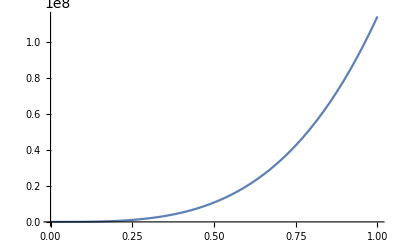

```mathematica
Plot[{Evaluate[f[t]]},{t,0,1}]
```

```mathematica
D2g[σ1_,t_]:=Evaluate[g[σ1,t]^2 D[Log[g[σ1,t]],t]];
D4g[σ1_,t_]:=Evaluate[D2g[σ1,t]^2 D[Log[D2g[σ1,t]],t]];
D8g[σ1_,t_]:=Evaluate[D4g[σ1,t]^2 D[Log[D4g[σ1,t]],t]];
```

```mathematica
term3[σ1_,t_] :=t g[σ1,t]^4(D2g[σ1,t])^3
term2[σ1_,t_]:=(D2g[σ1,t])(D4g[σ1,t])^2
term1[σ1_,t_]:=g[σ1,t]^2 D8g[σ1,t]
RHS[σ1_,t_]:=t^(1/4)(t^(-1/4)D2g[σ1,t])^3
```

```mathematica
RHS[σ1_,t_]:=t^(1/4)(t^(-1/4)D2g[σ1,t])^3
Tau23[σ1_,t_]:=t^(-3/4)(D4g[σ1,t])/g[σ1,t]
LHS[σ1_,t_]:=Evaluate[(Tau23[σ1,t])^2 D[Log[Tau23[σ1,t]],t]]
```

```mathematica
LHS[1,t]+O[t]
```

1/t^(3/4)(4627.51 t^0.680556+117158. t^1.00698+172108. t^1.19943+180.067 (1.+0.807279 t) t^1.35413+108399. t^1.48811+10474.6 t^1.87301+656.607 t^2.16168+61.7486 t^2.35413-3.12855×10^6 (1.+0.613534 t) t^2.39188+7.99532×10^7 t^2.52586+1.93048×10^7 t^2.81453-98247.6 (1.+0.415342 t) t^2.96923-565902. t^3.39188+747.212 (1.+0.565367 t) t^3.54658-10280.7 t^3.96923+92.9157 t^4.54658+6.65925 t^4.83526+886.648 t^1.16168 (1.+1.60083 t)+2.9809×10^7 t^1.81453 (1.+1.82273 t)+10.8349 t^3.83526 (1.+2.9718 t)+3950.76 t^0.873006 (1.+4.96589 t)+1.42692×10^7 t^1.52586 (1.+14.1529 t)+6844.11 t^0.488105 (1.+23.5691 t)+4008.6 t^0.19943 (1.+51.497 t)+2024.65 t^0.00698024 (1.+58.2698 t)+(0.680556 (1.+4627.51 t))/t^0.319444) ((4627.51 t^0.680556+117158. t^1.00698+172108. t^1.19943+180.067 (1.+0.807279 t) t^1.35413+108399. t^1.48811+10474.6 t^1.87301+656.607 t^2.16168+61.7486 t^2.35413-3.12855×10^6 (1.+0.613534 t) t^2.39188+7.99532×10^7 t^2.52586+1.93048×10^7 t^2.81453-98247.6 (1.+0.415342 t) t^2.96923-565902. t^3.39188+747.212 (1.+0.565367 t) t^3.54658-10280.7 t^3.96923+92.9157 t^4.54658+6.65925 t^4.83526+886.648 t^1.16168 (1.+1.60083 t)+2.9809×10^7 t^1.81453 (1.+1.82273 t)+10.8349 t^3.83526 (1.+2.9718 t)+3950.76 t^0.873006 (1.+4.96589 t)+1.42692×10^7 t^1.52586 (1.+14.1529 t)+6844.11 t^0.488105 (1.+23.5691 t)+4008.6 t^0.19943 (1.+51.497 t)+2024.65 t^0.00698024 (1.+58.2698 t)+(0.680556 (1.+4627.51 t))/t^0.319444)^2+(6298.56/t^0.319444+235951. t^0.00698024+412862. t^0.19943+243.834 (1.+0.807279 t) t^0.354131+322619. t^0.488105+39238.1 t^0.873006+2838.75 t^1.16168+290.729 t^1.35413-7.48312×10^6 (1.+0.613534 t) t^1.39188+4.03901×10^8 t^1.52586+1.08668×10^8 t^1.81453-291720. (1.+0.415342 t) t^1.96923-3.83894×10^6 t^2.39188+2650.05 (1.+0.565367 t) t^2.54658-81612.7 t^2.96923+844.898 t^3.54658+64.3983 t^3.83526+1030. t^0.161681 (1.+1.60083 t)+5.40893×10^7 t^0.81453 (1.+1.82273 t)+41.5547 t^2.83526 (1.+2.9718 t)+(3449.04 (1.+4.96589 t))/t^0.126994+2.17727×10^7 t^0.525855 (1.+14.1529 t)+(3340.65 (1.+23.5691 t))/t^0.511895+(799.437 (1.+51.497 t))/t^0.80057+(14.1325 (1.+58.2698 t))/t^0.99302-(0.2174 (1.+4627.51 t))/t^1.31944) (76.4898 (1.+0.807279 t) t^2.35413-922364. (1.+0.613534 t) t^3.39188-24752.3 (1.+0.415342 t) t^3.96923+164.346 (1.+0.565367 t) t^4.54658+410.166 t^2.16168 (1.+1.60083 t)+1.05911×10^7 t^2.81453 (1.+1.82273 t)+2.24082 t^4.83526 (1.+2.9718 t)+2109.32 t^1.87301 (1.+4.96589 t)+5.64925×10^6 t^2.52586 (1.+14.1529 t)+4599.21 t^1.48811 (1.+23.5691 t)+3342.09 t^1.19943 (1.+51.497 t)+2010.61 t^1.00698 (1.+58.2698 t)+t^0.680556 (1.+4627.51 t))) (1/t^(3/4)(4627.51 t^0.680556+117158. t^1.00698+172108. t^1.19943+180.067 (1.+0.807279 t) t^1.35413+108399. t^1.48811+10474.6 t^1.87301+656.607 t^2.16168+61.7486 t^2.35413-3.12855×10^6 (1.+0.613534 t) t^2.39188+7.99532×10^7 t^2.52586+1.93048×10^7 t^2.81453-98247.6 (1.+0.415342 t) t^2.96923-565902. t^3.39188+747.212 (1.+0.565367 t) t^3.54658-10280.7 t^3.96923+92.9157 t^4.54658+6.65925 t^4.83526+886.648 t^1.16168 (1.+1.60083 t)+2.9809×10^7 t^1.81453 (1.+1.82273 t)+10.8349 t^3.83526 (1.+2.9718 t)+3950.76 t^0.873006 (1.+4.96589 t)+1.42692×10^7 t^1.52586 (1.+14.1529 t)+6844.11 t^0.488105 (1.+23.5691 t)+4008.6 t^0.19943 (1.+51.497 t)+2024.65 t^0.00698024 (1.+58.2698 t)+(0.680556 (1.+4627.51 t))/t^0.319444) (3 (6298.56/t^0.319444+235951. t^0.00698024+412862. t^0.19943+243.834 (1.+0.807279 t) t^0.354131+322619. t^0.488105+39238.1 t^0.873006+2838.75 t^1.16168+290.729 t^1.35413-7.48312×10^6 (1.+0.613534 t) t^1.39188+4.03901×10^8 t^1.52586+1.08668×10^8 t^1.81453-291720. (1.+0.415342 t) t^1.96923-3.83894×10^6 t^2.39188+2650.05 (1.+0.565367 t) t^2.54658-81612.7 t^2.96923+844.898 t^3.54658+64.3983 t^3.83526+1030. t^0.161681 (1.+1.60083 t)+5.40893×10^7 t^0.81453 (1.+1.82273 t)+41.5547 t^2.83526 (1.+2.9718 t)+(3449.04 (1.+4.96589 t))/t^0.126994+2.17727×10^7 t^0.525855 (1.+14.1529 t)+(3340.65 (1.+23.5691 t))/t^0.511895+(799.437 (1.+51.497 t))/t^0.80057+(14.1325 (1.+58.2698 t))/t^0.99302-(0.2174 (1.+4627.51 t))/t^1.31944) (4627.51 t^0.680556+117158. t^1.00698+172108. t^1.19943+180.067 (1.+0.807279 t) t^1.35413+108399. t^1.48811+10474.6 t^1.87301+656.607 t^2.16168+61.7486 t^2.35413-3.12855×10^6 (1.+0.613534 t) t^2.39188+7.99532×10^7 t^2.52586+1.93048×10^7 t^2.81453-98247.6 (1.+0.415342 t) t^2.96923-565902. t^3.39188+747.212 (1.+0.565367 t) t^3.54658-10280.7 t^3.96923+92.9157 t^4.54658+6.65925 t^4.83526+886.648 t^1.16168 (1.+1.60083 t)+2.9809×10^7 t^1.81453 (1.+1.82273 t)+10.8349 t^3.83526 (1.+2.9718 t)+3950.76 t^0.873006 (1.+4.96589 t)+1.42692×10^7 t^1.52586 (1.+14.1529 t)+6844.11 t^0.488105 (1.+23.5691 t)+4008.6 t^0.19943 (1.+51.497 t)+2024.65 t^0.00698024 (1.+58.2698 t)+(0.680556 (1.+4627.51 t))/t^0.319444)+(-3018.06/t^1.31944+2470.5/t^0.99302+123506./t^0.80057+(86.3492 (1.+0.807279 t))/t^0.645869+236208./t^0.511895+51382.6/t^0.126994+4946.58 t^0.161681+590.527 t^0.354131-1.04156×10^7 (1.+0.613534 t) t^0.39188+9.2444×10^8 t^0.525855+2.95771×10^8 t^0.81453-574463. (1.+0.415342 t) t^0.969231-1.37734×10^7 t^1.39188+6748.56 (1.+0.565367 t) t^1.54658-363490. t^1.96923+4494.75 t^2.54658+370.476 t^2.83526+(166.532 (1.+1.60083 t))/t^0.838319+(4.40573×10^7 (1.+1.82273 t))/t^0.18547+117.818 t^1.83526 (1.+2.9718 t)-(438.008 (1.+4.96589 t))/t^1.12699+(1.14493×10^7 (1.+14.1529 t))/t^0.474145-(1710.06 (1.+23.5691 t))/t^1.51189-(640.005 (1.+51.497 t))/t^1.80057-(14.0339 (1.+58.2698 t))/t^1.99302+(0.286847 (1.+4627.51 t))/t^2.31944) (76.4898 (1.+0.807279 t) t^2.35413-922364. (1.+0.613534 t) t^3.39188-24752.3 (1.+0.415342 t) t^3.96923+164.346 (1.+0.565367 t) t^4.54658+410.166 t^2.16168 (1.+1.60083 t)+1.05911×10^7 t^2.81453 (1.+1.82273 t)+2.24082 t^4.83526 (1.+2.9718 t)+2109.32 t^1.87301 (1.+4.96589 t)+5.64925×10^6 t^2.52586 (1.+14.1529 t)+4599.21 t^1.48811 (1.+23.5691 t)+3342.09 t^1.19943 (1.+51.497 t)+2010.61 t^1.00698 (1.+58.2698 t)+t^0.680556 (1.+4627.51 t)))+1/t^(3/4)(6298.56/t^0.319444+235951. t^0.00698024+412862. t^0.19943+243.834 (1.+0.807279 t) t^0.354131+322619. t^0.488105+39238.1 t^0.873006+2838.75 t^1.16168+290.729 t^1.35413-7.48312×10^6 (1.+0.613534 t) t^1.39188+4.03901×10^8 t^1.52586+1.08668×10^8 t^1.81453-291720. (1.+0.415342 t) t^1.96923-3.83894×10^6 t^2.39188+2650.05 (1.+0.565367 t) t^2.54658-81612.7 t^2.96923+844.898 t^3.54658+64.3983 t^3.83526+1030. t^0.161681 (1.+1.60083 t)+5.40893×10^7 t^0.81453 (1.+1.82273 t)+41.5547 t^2.83526 (1.+2.9718 t)+(3449.04 (1.+4.96589 t))/t^0.126994+2.17727×10^7 t^0.525855 (1.+14.1529 t)+(3340.65 (1.+23.5691 t))/t^0.511895+(799.437 (1.+51.497 t))/t^0.80057+(14.1325 (1.+58.2698 t))/t^0.99302-(0.2174 (1.+4627.51 t))/t^1.31944) ((4627.51 t^0.680556+117158. t^1.00698+172108. t^1.19943+180.067 (1.+0.807279 t) t^1.35413+108399. t^1.48811+10474.6 t^1.87301+656.607 t^2.16168+61.7486 t^2.35413-3.12855×10^6 (1.+0.613534 t) t^2.39188+7.99532×10^7 t^2.52586+1.93048×10^7 t^2.81453-98247.6 (1.+0.415342 t) t^2.96923-565902. t^3.39188+747.212 (1.+0.565367 t) t^3.54658-10280.7 t^3.96923+92.9157 t^4.54658+6.65925 t^4.83526+886.648 t^1.16168 (1.+1.60083 t)+2.9809×10^7 t^1.81453 (1.+1.82273 t)+10.8349 t^3.83526 (1.+2.9718 t)+3950.76 t^0.873006 (1.+4.96589 t)+1.42692×10^7 t^1.52586 (1.+14.1529 t)+6844.11 t^0.488105 (1.+23.5691 t)+4008.6 t^0.19943 (1.+51.497 t)+2024.65 t^0.00698024 (1.+58.2698 t)+(0.680556 (1.+4627.51 t))/t^0.319444)^2+(6298.56/t^0.319444+235951. t^0.00698024+412862. t^0.19943+243.834 (1.+0.807279 t) t^0.354131+322619. t^0.488105+39238.1 t^0.873006+2838.75 t^1.16168+290.729 t^1.35413-7.48312×10^6 (1.+0.613534 t) t^1.39188+4.03901×10^8 t^1.52586+1.08668×10^8 t^1.81453-291720. (1.+0.415342 t) t^1.96923-3.83894×10^6 t^2.39188+2650.05 (1.+0.565367 t) t^2.54658-81612.7 t^2.96923+844.898 t^3.54658+64.3983 t^3.83526+1030. t^0.161681 (1.+1.60083 t)+5.40893×10^7 t^0.81453 (1.+1.82273 t)+41.5547 t^2.83526 (1.+2.9718 t)+(3449.04 (1.+4.96589 t))/t^0.126994+2.17727×10^7 t^0.525855 (1.+14.1529 t)+(3340.65 (1.+23.5691 t))/t^0.511895+(799.437 (1.+51.497 t))/t^0.80057+(14.1325 (1.+58.2698 t))/t^0.99302-(0.2174 (1.+4627.51 t))/t^1.31944) (76.4898 (1.+0.807279 t) t^2.35413-922364. (1.+0.613534 t) t^3.39188-24752.3 (1.+0.415342 t) t^3.96923+164.346 (1.+0.565367 t) t^4.54658+410.166 t^2.16168 (1.+1.60083 t)+1.05911×10^7 t^2.81453 (1.+1.82273 t)+2.24082 t^4.83526 (1.+2.9718 t)+2109.32 t^1.87301 (1.+4.96589 t)+5.64925×10^6 t^2.52586 (1.+14.1529 t)+4599.21 t^1.48811 (1.+23.5691 t)+3342.09 t^1.19943 (1.+51.497 t)+2010.61 t^1.00698 (1.+58.2698 t)+t^0.680556 (1.+4627.51 t)))-1/(4 t^(7/4))3 (4627.51 t^0.680556+117158. t^1.00698+172108. t^1.19943+180.067 (1.+0.807279 t) t^1.35413+108399. t^1.48811+10474.6 t^1.87301+656.607 t^2.16168+61.7486 t^2.35413-3.12855×10^6 (1.+0.613534 t) t^2.39188+7.99532×10^7 t^2.52586+1.93048×10^7 t^2.81453-98247.6 (1.+0.415342 t) t^2.96923-565902. t^3.39188+747.212 (1.+0.565367 t) t^3.54658-10280.7 t^3.96923+92.9157 t^4.54658+6.65925 t^4.83526+886.648 t^1.16168 (1.+1.60083 t)+2.9809×10^7 t^1.81453 (1.+1.82273 t)+10.8349 t^3.83526 (1.+2.9718 t)+3950.76 t^0.873006 (1.+4.96589 t)+1.42692×10^7 t^1.52586 (1.+14.1529 t)+6844.11 t^0.488105 (1.+23.5691 t)+4008.6 t^0.19943 (1.+51.497 t)+2024.65 t^0.00698024 (1.+58.2698 t)+(0.680556 (1.+4627.51 t))/t^0.319444) ((4627.51 t^0.680556+117158. t^1.00698+172108. t^1.19943+180.067 (1.+0.807279 t) t^1.35413+108399. t^1.48811+10474.6 t^1.87301+656.607 t^2.16168+61.7486 t^2.35413-3.12855×10^6 (1.+0.613534 t) t^2.39188+7.99532×10^7 t^2.52586+1.93048×10^7 t^2.81453-98247.6 (1.+0.415342 t) t^2.96923-565902. t^3.39188+747.212 (1.+0.565367 t) t^3.54658-10280.7 t^3.96923+92.9157 t^4.54658+6.65925 t^4.83526+886.648 t^1.16168 (1.+1.60083 t)+2.9809×10^7 t^1.81453 (1.+1.82273 t)+10.8349 t^3.83526 (1.+2.9718 t)+3950.76 t^0.873006 (1.+4.96589 t)+1.42692×10^7 t^1.52586 (1.+14.1529 t)+6844.11 t^0.488105 (1.+23.5691 t)+4008.6 t^0.19943 (1.+51.497 t)+2024.65 t^0.00698024 (1.+58.2698 t)+(0.680556 (1.+4627.51 t))/t^0.319444)^2+(6298.56/t^0.319444+235951. t^0.00698024+412862. t^0.19943+243.834 (1.+0.807279 t) t^0.354131+322619. t^0.488105+39238.1 t^0.873006+2838.75 t^1.16168+290.729 t^1.35413-7.48312×10^6 (1.+0.613534 t) t^1.39188+4.03901×10^8 t^1.52586+1.08668×10^8 t^1.81453-291720. (1.+0.415342 t) t^1.96923-3.83894×10^6 t^2.39188+2650.05 (1.+0.565367 t) t^2.54658-81612.7 t^2.96923+844.898 t^3.54658+64.3983 t^3.83526+1030. t^0.161681 (1.+1.60083 t)+5.40893×10^7 t^0.81453 (1.+1.82273 t)+41.5547 t^2.83526 (1.+2.9718 t)+(3449.04 (1.+4.96589 t))/t^0.126994+2.17727×10^7 t^0.525855 (1.+14.1529 t)+(3340.65 (1.+23.5691 t))/t^0.511895+(799.437 (1.+51.497 t))/t^0.80057+(14.1325 (1.+58.2698 t))/t^0.99302-(0.2174 (1.+4627.51 t))/t^1.31944) (76.4898 (1.+0.807279 t) t^2.35413-922364. (1.+0.613534 t) t^3.39188-24752.3 (1.+0.415342 t) t^3.96923+164.346 (1.+0.565367 t) t^4.54658+410.166 t^2.16168 (1.+1.60083 t)+1.05911×10^7 t^2.81453 (1.+1.82273 t)+2.24082 t^4.83526 (1.+2.9718 t)+2109.32 t^1.87301 (1.+4.96589 t)+5.64925×10^6 t^2.52586 (1.+14.1529 t)+4599.21 t^1.48811 (1.+23.5691 t)+3342.09 t^1.19943 (1.+51.497 t)+2010.61 t^1.00698 (1.+58.2698 t)+t^0.680556 (1.+4627.51 t))))+O[t]^1

```mathematica
RHS[1,t]//Simplify
```

```mathematica
term3[σ1_,t_] := t^(-4.35)g[σ1,t]^4(D2g[σ1,t])^3
```

```mathematica
9/2//N
```

4.5

```mathematica
Plot[Evaluate[RHS[σ1,0.001]],{σ1,0.8,1.2}]
```

-Graphics-

```mathematica
Plot[{Evaluate[term1[σ1,0.001]],Evaluate[term2[σ1,0.001]],Evaluate[term3[σ1,0.001]]},{σ1,0.8,1.2}]
```

-Graphics-

```mathematica
Plot[{Evaluate[term1[σ1,0.001]-term2[σ1,0.001]],Evaluate[term3[σ1,0.001]]},{σ1,0.8,1.2}]
```

-Graphics-

```mathematica
Plot[{Evaluate[LHS[σ1,0.001]],Evaluate[RHS[σ1,0.001]]},{σ1,0.2,0.9}]
```

-Graphics-

```mathematica
Plot[Evaluate[term1[σ1,0.001]-term2[σ1,0.001]-term3[σ1,0.001]],{σ1,0.7,2}]
```

-Graphics-

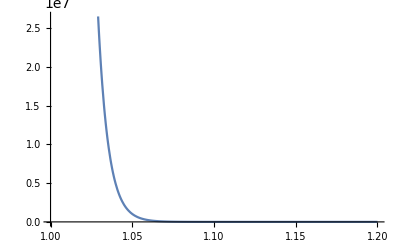

```mathematica
Plot[Evaluate[term1[σ1,0.001]-term2[σ1,0.001]-term3[σ1,0.001]],{σ1,1.0,1.2}]
```

```mathematica
Plot[Evaluate[term1[1,t]-term2[1,t]-term3[1,t]],{t,0.01,0.90}]
```

-Graphics-